## Dipole v2, |J|^2 at large kT

```mathematica
Quit[]
```

### |J|^2 at large kT

```mathematica
ClearAll[SP];
SP[x_]:=SP[x,x];
SP[x_,y1_+y2_]:=SP[x,y1]+SP[x,y2];
SP[x1_+x2_,y_]:=SP[x1,y]+SP[x2,y];
SP[x_,-y_]:=-SP[x,y];
SP[-x_,y_]:=-SP[x,y];
SP[x_,k]/;!FreeQ[{x1,x2,x3,x4},x]:=SP[k,x];
SP[x_,x1]/;!FreeQ[{x2,x3,x4},x]:=SP[x1,x];
SP[x_,x2]/;!FreeQ[{x3,x4},x]:=SP[x2,x];
SP[x4,x3]:=SP[x3,x4];
SP[ϵ x_,y_]:=ϵ SP[x,y];
SP[x_,ϵ y_]:=ϵ SP[x,y];
```

```mathematica
ClearAll[MyresT1];
MyresT1=2/(2π)^2 1/SP[k]^2((1+cb31)/b31^2+(1+cb41)/b41^2+(1+cb32)/b32^2+(1+cb42)/b42^2+(x34^2-b31^2-b41^2)/(2 b31^2 b41^2)(1+cb31+cb41+c34)+(x12^2-b31^2-b32^2)/(2 b31^2 b32^2)(1+cb31+cb32+c12)-(x1432^2-b31^2-b42^2)/(2 b31^2 b42^2)(c12+cb32+cb41+c34)-(x1342^2-b41^2-b32^2)/(2 b32^2 b41^2)(c12+cb42+cb31+c34)+(x12^2-b41^2-b42^2)/(2 b41^2 b42^2)(1+cb41+cb42+c12)+(x34^2-b32^2-b42^2)/(2 b32^2 b42^2)(1+cb32+cb42+c34));
```

```mathematica
ClearAll[MyresT2];
MyresT2=-1/π^2 1/SP[k]^3((SP[k,x31]/SP[x31]-SP[k,x41]/SP[x41])(SP[k,x31]/SP[x31]-SP[k,x32]/SP[x32])c31-(SP[k,x32]/SP[x32]-SP[k,x42]/SP[x42])(SP[k,x31]/SP[x31]-SP[k,x32]/SP[x32])c32-(SP[k,x31]/SP[x31]-SP[k,x41]/SP[x41])(SP[k,x41]/SP[x41]-SP[k,x42]/SP[x42])c41+(SP[k,x32]/SP[x32]-SP[k,x42]/SP[x42])(SP[k,x41]/SP[x41]-SP[k,x42]/SP[x42])c42);
```

```mathematica
ClearAll[Myres];
Myres=MyresT1+MyresT2/.{cb31:>c31,cb41:>c41,cb32:>c32,cb42:>c42,b31:>√SP[x31],b32:>√SP[x32],b41:>√SP[x41],b42:>√SP[x42],x1432:>√SP[x1432],x1342:>√SP[x1342],x12:>√SP[x12],x34:>√SP[x34]}/.{x1342:>x32-x41,x1432:>x42-x31}/.{c31:>Cos[SP[k,x31]],c32:>Cos[SP[k,x32]],c12:>Cos[SP[k,x12]],c41:>Cos[SP[k,x41]],c42:>Cos[SP[k,x42]],c34:>Cos[SP[k,x34]]};
```

```mathematica
Myres
```

-1/(π^2 SP[k,k]^3)(Cos[SP[k,x31]] (SP[k,x31]/SP[x31,x31]-SP[k,x32]/SP[x32,x32]) (SP[k,x31]/SP[x31,x31]-SP[k,x41]/SP[x41,x41])-Cos[SP[k,x32]] (SP[k,x31]/SP[x31,x31]-SP[k,x32]/SP[x32,x32]) (SP[k,x32]/SP[x32,x32]-SP[k,x42]/SP[x42,x42])-Cos[SP[k,x41]] (SP[k,x31]/SP[x31,x31]-SP[k,x41]/SP[x41,x41]) (SP[k,x41]/SP[x41,x41]-SP[k,x42]/SP[x42,x42])+Cos[SP[k,x42]] (SP[k,x32]/SP[x32,x32]-SP[k,x42]/SP[x42,x42]) (SP[k,x41]/SP[x41,x41]-SP[k,x42]/SP[x42,x42]))+1/(2 π^2 SP[k,k]^2)((1+Cos[SP[k,x31]])/SP[x31,x31]+(1+Cos[SP[k,x32]])/SP[x32,x32]+((1+Cos[SP[k,x12]]+Cos[SP[k,x31]]+Cos[SP[k,x32]]) (SP[x12,x12]-SP[x31,x31]-SP[x32,x32]))/(2 SP[x31,x31] SP[x32,x32])+(1+Cos[SP[k,x41]])/SP[x41,x41]-((Cos[SP[k,x12]]+Cos[SP[k,x31]]+Cos[SP[k,x34]]+Cos[SP[k,x42]]) (-SP[x32,x41]-SP[x41,x32]))/(2 SP[x32,x32] SP[x41,x41])+((1+Cos[SP[k,x31]]+Cos[SP[k,x34]]+Cos[SP[k,x41]]) (-SP[x31,x31]+SP[x34,x34]-SP[x41,x41]))/(2 SP[x31,x31] SP[x41,x41])+(1+Cos[SP[k,x42]])/SP[x42,x42]-((Cos[SP[k,x12]]+Cos[SP[k,x32]]+Cos[SP[k,x34]]+Cos[SP[k,x41]]) (-SP[x31,x42]-SP[x42,x31]))/(2 SP[x31,x31] SP[x42,x42])+((1+Cos[SP[k,x32]]+Cos[SP[k,x34]]+Cos[SP[k,x42]]) (-SP[x32,x32]+SP[x34,x34]-SP[x42,x42]))/(2 SP[x32,x32] SP[x42,x42])+((1+Cos[SP[k,x12]]+Cos[SP[k,x41]]+Cos[SP[k,x42]]) (SP[x12,x12]-SP[x41,x41]-SP[x42,x42]))/(2 SP[x41,x41] SP[x42,x42]))

```mathematica
Variables[Myres/.SP[x_,y_]:>x y/.Cos[x_]:>x]
```

{k,x31,x32,x41,x42,x12,x34}

```mathematica
ClearAll[INT];
INT[x_*y_]/;FreeQ[x,SP[k,x31]|SP[k,x32]|SP[k,x41]|SP[k,x42]|SP[k,x12]|SP[k,x34]]:=x*INT[y];
INT[x_+y_]:=INT[x]+INT[y];
INT[x_]/;x=!=1&&FreeQ[x,SP[k,x31]|SP[k,x32]|SP[k,x41]|SP[k,x42]|SP[k,x12]|SP[k,x34]]:=x*INT[1]
```

```mathematica
ClearAll[Myres1];
Myres1=INT[Myres//Expand]
```

-INT[Cos[SP[k,x31]] SP[k,x31]^2]/(π^2 SP[k,k]^3 SP[x31,x31]^2)-INT[Cos[SP[k,x12]]]/(4 π^2 SP[k,k]^2 SP[x31,x31])-INT[Cos[SP[k,x32]]]/(4 π^2 SP[k,k]^2 SP[x31,x31])-INT[Cos[SP[k,x34]]]/(4 π^2 SP[k,k]^2 SP[x31,x31])-INT[Cos[SP[k,x41]]]/(4 π^2 SP[k,k]^2 SP[x31,x31])-INT[Cos[SP[k,x32]] SP[k,x32]^2]/(π^2 SP[k,k]^3 SP[x32,x32]^2)-INT[Cos[SP[k,x12]]]/(4 π^2 SP[k,k]^2 SP[x32,x32])-INT[Cos[SP[k,x31]]]/(4 π^2 SP[k,k]^2 SP[x32,x32])-INT[Cos[SP[k,x34]]]/(4 π^2 SP[k,k]^2 SP[x32,x32])-INT[Cos[SP[k,x42]]]/(4 π^2 SP[k,k]^2 SP[x32,x32])+INT[Cos[SP[k,x31]] SP[k,x31] SP[k,x32]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x32,x32])+INT[Cos[SP[k,x32]] SP[k,x31] SP[k,x32]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x32,x32])+(INT[1] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x32,x32])+(INT[Cos[SP[k,x12]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x32,x32])+(INT[Cos[SP[k,x31]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x32,x32])+(INT[Cos[SP[k,x32]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x32,x32])-INT[Cos[SP[k,x41]] SP[k,x41]^2]/(π^2 SP[k,k]^3 SP[x41,x41]^2)-INT[Cos[SP[k,x12]]]/(4 π^2 SP[k,k]^2 SP[x41,x41])-INT[Cos[SP[k,x31]]]/(4 π^2 SP[k,k]^2 SP[x41,x41])-INT[Cos[SP[k,x34]]]/(4 π^2 SP[k,k]^2 SP[x41,x41])-INT[Cos[SP[k,x42]]]/(4 π^2 SP[k,k]^2 SP[x41,x41])+INT[Cos[SP[k,x31]] SP[k,x31] SP[k,x41]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x41,x41])+INT[Cos[SP[k,x41]] SP[k,x31] SP[k,x41]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x41,x41])-INT[Cos[SP[k,x31]] SP[k,x32] SP[k,x41]]/(π^2 SP[k,k]^3 SP[x32,x32] SP[x41,x41])-INT[Cos[SP[k,x42]] SP[k,x32] SP[k,x41]]/(π^2 SP[k,k]^3 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x12]]] SP[x32,x41])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x31]]] SP[x32,x41])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x34]]] SP[x32,x41])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x42]]] SP[x32,x41])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[1] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x41,x41])+(INT[Cos[SP[k,x31]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x41,x41])+(INT[Cos[SP[k,x34]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x41,x41])+(INT[Cos[SP[k,x41]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x41,x41])+(INT[Cos[SP[k,x12]]] SP[x41,x32])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x31]]] SP[x41,x32])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x34]]] SP[x41,x32])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])+(INT[Cos[SP[k,x42]]] SP[x41,x32])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x41,x41])-INT[Cos[SP[k,x42]] SP[k,x42]^2]/(π^2 SP[k,k]^3 SP[x42,x42]^2)-INT[Cos[SP[k,x12]]]/(4 π^2 SP[k,k]^2 SP[x42,x42])-INT[Cos[SP[k,x32]]]/(4 π^2 SP[k,k]^2 SP[x42,x42])-INT[Cos[SP[k,x34]]]/(4 π^2 SP[k,k]^2 SP[x42,x42])-INT[Cos[SP[k,x41]]]/(4 π^2 SP[k,k]^2 SP[x42,x42])-INT[Cos[SP[k,x32]] SP[k,x31] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x42,x42])-INT[Cos[SP[k,x41]] SP[k,x31] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x12]]] SP[x31,x42])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x32]]] SP[x31,x42])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x34]]] SP[x31,x42])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x41]]] SP[x31,x42])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+INT[Cos[SP[k,x32]] SP[k,x32] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x32,x32] SP[x42,x42])+INT[Cos[SP[k,x42]] SP[k,x32] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x32,x32] SP[x42,x42])+(INT[1] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x42,x42])+(INT[Cos[SP[k,x32]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x42,x42])+(INT[Cos[SP[k,x34]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x42,x42])+(INT[Cos[SP[k,x42]]] SP[x34,x34])/(4 π^2 SP[k,k]^2 SP[x32,x32] SP[x42,x42])+INT[Cos[SP[k,x41]] SP[k,x41] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x41,x41] SP[x42,x42])+INT[Cos[SP[k,x42]] SP[k,x41] SP[k,x42]]/(π^2 SP[k,k]^3 SP[x41,x41] SP[x42,x42])+(INT[1] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x41,x41] SP[x42,x42])+(INT[Cos[SP[k,x12]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x41,x41] SP[x42,x42])+(INT[Cos[SP[k,x41]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x41,x41] SP[x42,x42])+(INT[Cos[SP[k,x42]]] SP[x12,x12])/(4 π^2 SP[k,k]^2 SP[x41,x41] SP[x42,x42])+(INT[Cos[SP[k,x12]]] SP[x42,x31])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x32]]] SP[x42,x31])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x34]]] SP[x42,x31])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])+(INT[Cos[SP[k,x41]]] SP[x42,x31])/(4 π^2 SP[k,k]^2 SP[x31,x31] SP[x42,x42])

```mathematica
Myres1//Variables//Select[#,#1[[0]]===INT&]&//Sort
```

{INT[1],INT[Cos[SP[k,x12]]],INT[Cos[SP[k,x31]]],INT[Cos[SP[k,x32]]],INT[Cos[SP[k,x34]]],INT[Cos[SP[k,x41]]],INT[Cos[SP[k,x42]]],INT[Cos[SP[k,x31]] SP[k,x31]^2],INT[Cos[SP[k,x31]] SP[k,x31] SP[k,x32]],INT[Cos[SP[k,x32]] SP[k,x31] SP[k,x32]],INT[Cos[SP[k,x32]] SP[k,x32]^2],INT[Cos[SP[k,x31]] SP[k,x31] SP[k,x41]],INT[Cos[SP[k,x41]] SP[k,x31] SP[k,x41]],INT[Cos[SP[k,x31]] SP[k,x32] SP[k,x41]],INT[Cos[SP[k,x42]] SP[k,x32] SP[k,x41]],INT[Cos[SP[k,x41]] SP[k,x41]^2],INT[Cos[SP[k,x32]] SP[k,x31] SP[k,x42]],INT[Cos[SP[k,x41]] SP[k,x31] SP[k,x42]],INT[Cos[SP[k,x32]] SP[k,x32] SP[k,x42]],INT[Cos[SP[k,x42]] SP[k,x32] SP[k,x42]],INT[Cos[SP[k,x41]] SP[k,x41] SP[k,x42]],INT[Cos[SP[k,x42]] SP[k,x41] SP[k,x42]],INT[Cos[SP[k,x42]] SP[k,x42]^2]}

```mathematica
Myres1//Variables//Select[#,#1[[0]]=!=INT&]&//Sort
```

{SP[k,k],SP[x12,x12],SP[x31,x31],SP[x31,x42],SP[x32,x32],SP[x32,x41],SP[x34,x34],SP[x41,x32],SP[x41,x41],SP[x42,x31],SP[x42,x42]}

```mathematica
ClearAll[Toθ];
Toθ[x_]:=StringJoin["θ",ToString[x]//StringDrop[#,1]&]//ToExpression;
```

```mathematica
ClearAll[rplcSigma];
rplcSigma={INT2[1]:>2π,INT2[Cos[SP[k,x_]]]:>2π BesselJ[0,A[k]A[x]],INT2[Cos[SP[k,x1_]]SP[k,x2_]SP[k,x3_]]:>A[k]^2 A[x2]A[x3]((2π)/(A[k]A[x1])BesselJ[1,A[k]A[x1]]Cos[Toθ[x2]-Toθ[x3]]-2π BesselJ[2,A[k]A[x1]]Cos[Toθ[x2]-Toθ[x1]]Cos[Toθ[x3]-Toθ[x1]]),
INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>A[k]^2 A[x2]^2((2π)/(A[k]A[x1])BesselJ[1,A[k]A[x1]]-2π BesselJ[2,A[k]A[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)}
```

{INT2[1]:>2 π,INT2[Cos[SP[k,x_]]]:>2 π BesselJ[0,A[k] A[x]],INT2[Cos[SP[k,x1_]] SP[k,x2_] SP[k,x3_]]:>A[k]^2 A[x2] A[x3] (((2 π) BesselJ[1,A[k] A[x1]] Cos[Toθ[x2]-Toθ[x3]])/(A[k] A[x1])-2 π BesselJ[2,A[k] A[x1]] Cos[Toθ[x2]-Toθ[x1]] Cos[Toθ[x3]-Toθ[x1]]),INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>A[k]^2 A[x2]^2 (((2 π) BesselJ[1,A[k] A[x1]])/(A[k] A[x1])-2 π BesselJ[2,A[k] A[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)}

```mathematica
ClearAll[rplc0];
rplc0={SP[x42,x31]:>SP[x31,x42],SP[x41,x32]:>SP[x32,x41],SP[x_,x_]:>A[x]^2};
```

```mathematica
ClearAll[σAvg];
σAvg=Myres1/.INT:>INT2/.rplcSigma/.rplc0//Together;
```

```mathematica
ClearAll[rplcV2];
rplcV2={INT2[1]:>0,INT2[Cos[SP[k,x_]]]:>-2π BesselJ[2,A[k]A[x]]Cos[2Toθ[x]],INT2[Cos[SP[k,x1_]]SP[k,x2_]SP[k,x3_]]:>A[x2]A[x3] π/A[x1]^2(2BesselJ[2,A[k]A[x1]](6Cos[Toθ[x2]+Toθ[x3]-4Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2Toθ[x1]]Cos[Toθ[x2]-Toθ[x1]]Cos[Toθ[x3]-Toθ[x1]])+A[k]A[x1]BesselJ[1,A[k]A[x1]](Cos[Toθ[x2]+Toθ[x3]]-3Cos[Toθ[x2]+Toθ[x3]-4Toθ[x1]])),
INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>A[x2]^2 π/A[x1]^2(2BesselJ[2,A[k]A[x1]](6Cos[2Toθ[x2]-4Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2Toθ[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)+A[k]A[x1]BesselJ[1,A[k]A[x1]](Cos[2Toθ[x2]]-3Cos[2Toθ[x2]-4Toθ[x1]]))}
```

{INT2[1]:>0,INT2[Cos[SP[k,x_]]]:>-2 π BesselJ[2,A[k] A[x]] Cos[2 Toθ[x]],INT2[Cos[SP[k,x1_]] SP[k,x2_] SP[k,x3_]]:>1/A[x1]^2 A[x2] A[x3] π (2 BesselJ[2,A[k] A[x1]] (6 Cos[Toθ[x2]+Toθ[x3]-4 Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2 Toθ[x1]] Cos[Toθ[x2]-Toθ[x1]] Cos[Toθ[x3]-Toθ[x1]])+A[k] A[x1] BesselJ[1,A[k] A[x1]] (Cos[Toθ[x2]+Toθ[x3]]-3 Cos[Toθ[x2]+Toθ[x3]-4 Toθ[x1]])),INT2[Cos[SP[k,x1_]] SP[k,x2_]^2]:>(A[x2]^2 π (2 BesselJ[2,A[k] A[x1]] (6 Cos[2 Toθ[x2]-4 Toθ[x1]]-A[k]^2 A[x1]^2 Cos[2 Toθ[x1]] Cos[Toθ[x2]-Toθ[x1]]^2)+A[k] A[x1] BesselJ[1,A[k] A[x1]] (Cos[2 Toθ[x2]]-3 Cos[2 Toθ[x2]-4 Toθ[x1]])))/A[x1]^2}

```mathematica
ClearAll[Avg2θk];
Avg2θk=Myres1/.INT:>INT2/.rplcV2/.rplc0//Together;
```

```mathematica
ClearAll[VarσAvg];
VarσAvg=Variables[σAvg]/.BesselJ[_,x_]:>x/.Cos[x_]:>x//Variables//DeleteDuplicates//Sort
```

{θ31,θ32,θ41,θ42,A[k],A[x12],A[x31],A[x32],A[x34],A[x41],A[x42],SP[x31,x42],SP[x32,x41]}

```mathematica
ClearAll[VarAvg2θk];
VarAvg2θk=Variables[Avg2θk]/.BesselJ[_,x_]:>x/.Cos[x_]:>x//Variables//DeleteDuplicates//Sort
```

{θ12,θ31,θ32,θ34,θ41,θ42,A[k],A[x12],A[x31],A[x32],A[x34],A[x41],A[x42],SP[x31,x42],SP[x32,x41]}

```mathematica
SubsetQ[VarAvg2θk,VarσAvg]
```

True

### Create Code Input

```mathematica
σAvg//InputForm
```

(A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42] + A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42] + A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3 + A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3 + 
  A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0, A[k]*A[x12]] - A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x12]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x12]] + A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x12]] - 
  A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x12]] - A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x12]] - A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x31]] + 
  A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x31]] + A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x31]] - 
  A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x31]] - A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x32]] + 
  A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x32]] + A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x32]] - 
  A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x32]] - A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x34]] + 
  A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x34]] - A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x34]] + 
  A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x34]] - A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x34]] - 
  A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x34]] + A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0, A[k]*A[x41]] - 
  A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x41]] + A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x41]] - 
  A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x41]] + A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0, A[k]*A[x42]] + 
  A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x42]] - A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x42]] - 
  A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0, A[k]*A[x42]] - 4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x31]] - 4*A[x31]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x32]] - 
  4*A[x31]^3*A[x32]^3*A[x42]^3*BesselJ[1, A[k]*A[x41]] - 4*A[x31]^3*A[x32]^3*A[x41]^3*BesselJ[1, A[k]*A[x42]] + 4*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x31]] + 
  4*A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x32]] + 4*A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[2, A[k]*A[x41]] + 
  4*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[2, A[k]*A[x42]] + 4*A[x31]*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x31]]*Cos[θ31 - θ32] + 
  4*A[x31]^2*A[x32]*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - θ32] - 4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x31]]*Cos[θ31 - θ32] - 
  4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32] + 4*A[x31]*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x31]]*Cos[θ31 - θ41] + 
  4*A[x31]^2*A[x32]^3*A[x41]*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - θ41] - 4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x31]]*Cos[θ31 - θ41] - 
  4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41] + 4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x31]]*Cos[θ31 - θ32]*Cos[θ31 - θ41] - 
  4*A[x31]^2*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x31]]*Cos[θ32 - θ41] - 4*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ32 - θ41] - 
  4*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - θ42] - 4*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - θ42] + 
  4*A[x31]^3*A[x32]*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x32]]*Cos[θ32 - θ42] + 4*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]*BesselJ[1, A[k]*A[x42]]*Cos[θ32 - θ42] - 
  4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[θ32 - θ42] - 4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42] + 
  4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32]*Cos[θ32 - θ42] + 4*A[x31]^3*A[x32]^3*A[x41]*A[x42]^2*BesselJ[1, A[k]*A[x41]]*Cos[θ41 - θ42] + 
  4*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]*BesselJ[1, A[k]*A[x42]]*Cos[θ41 - θ42] - 4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[θ41 - θ42] - 
  4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[θ41 - θ42] + 4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41]*Cos[θ41 - θ42] + 
  4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42]*Cos[θ41 - θ42] + 2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x12]]*SP[x31, x42] + 
  2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x32]]*SP[x31, x42] + 2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x34]]*SP[x31, x42] + 
  2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0, A[k]*A[x41]]*SP[x31, x42] + 2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x12]]*SP[x32, x41] + 
  2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x31]]*SP[x32, x41] + 2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x34]]*SP[x32, x41] + 
  2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0, A[k]*A[x42]]*SP[x32, x41])/(2*Pi*A[k]^5*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^3)

```mathematica
Avg2θk//InputForm
```

(-(A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12]) + A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] - A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12] + 
  4*A[k]*A[x31]*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[2*θ31] + A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - 
  A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - 24*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] + 
  4*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31] - 6*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - 3*θ32] + 
  24*A[x31]^3*A[x32]*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - 3*θ32] - 4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31 - θ32] - 
  6*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[3*θ31 - θ32] + 24*A[x31]*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[3*θ31 - θ32] + 
  4*A[k]*A[x31]^4*A[x32]*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x32]]*Cos[2*θ32] + A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 
  A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 24*A[x31]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 
  A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] + 4*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] + 
  A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32] - 4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32]*Cos[2*θ32] + 
  2*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[θ31 + θ32] + 2*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1, A[k]*A[x32]]*Cos[θ31 + θ32] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] - A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] + 
  A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] - A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] + A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34] - 
  6*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - 3*θ41] + 24*A[x31]^3*A[x32]^4*A[x41]*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - 3*θ41] - 
  4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31 - θ41] + 4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*
   Cos[θ31 - θ32]*Cos[θ31 - θ41] - 6*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[3*θ31 - θ41] + 
  24*A[x31]*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[3*θ31 - θ41] + 6*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[4*θ31 - θ32 - θ41] - 
  24*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[4*θ31 - θ32 - θ41] + 4*A[k]*A[x31]^4*A[x32]^4*A[x41]*A[x42]^4*BesselJ[1, A[k]*A[x41]]*Cos[2*θ41] - 
  A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] + A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] - 
  24*A[x31]^4*A[x32]^4*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] + 4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] - 
  A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] + A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41] - 
  4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41]*Cos[2*θ41] + 2*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[θ31 + θ41] + 
  2*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1, A[k]*A[x41]]*Cos[θ31 + θ41] - 2*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1, A[k]*A[x31]]*Cos[θ32 + θ41] - 
  2*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x42]]*Cos[θ32 + θ41] + 6*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x42]]*Cos[θ32 + θ41 - 4*θ42] - 
  24*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[θ32 + θ41 - 4*θ42] - 6*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ32 - 3*θ42] + 
  24*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - 3*θ42] - 6*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x42]]*Cos[θ41 - 3*θ42] + 
  24*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]*BesselJ[2, A[k]*A[x42]]*Cos[θ41 - 3*θ42] - 4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[2*θ32]*Cos[θ32 - θ42] + 
  4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[θ31 - θ32]*Cos[2*θ32]*Cos[θ32 - θ42] - 6*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*
   Cos[3*θ32 - θ42] + 24*A[x31]^4*A[x32]*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*Cos[3*θ32 - θ42] - 4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41]*
   Cos[θ41 - θ42] + 4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[θ31 - θ41]*Cos[2*θ41]*Cos[θ41 - θ42] - 
  6*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[3*θ41 - θ42] + 24*A[x31]^4*A[x32]^4*A[x41]*A[x42]^3*BesselJ[2, A[k]*A[x41]]*Cos[3*θ41 - θ42] + 
  4*A[k]*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]*BesselJ[1, A[k]*A[x42]]*Cos[2*θ42] - 24*A[x31]^4*A[x32]^4*A[x41]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] - 
  A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] + 4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] - 
  A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] + A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] + 
  A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42] - 4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42]*Cos[2*θ42] - 
  4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2, A[k]*A[x42]]*Cos[θ41 - θ42]*Cos[2*θ42] + 4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2, A[k]*A[x42]]*Cos[θ32 - θ42]*
   Cos[θ41 - θ42]*Cos[2*θ42] - 2*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ31 + θ42] - 2*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x41]]*
   Cos[θ31 + θ42] + 6*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ31 - 4*θ32 + θ42] - 24*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[2, A[k]*A[x32]]*
   Cos[θ31 - 4*θ32 + θ42] + 2*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1, A[k]*A[x32]]*Cos[θ32 + θ42] + 2*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1, A[k]*A[x42]]*
   Cos[θ32 + θ42] + 6*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[θ31 - 4*θ41 + θ42] - 24*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[2, A[k]*A[x41]]*
   Cos[θ31 - 4*θ41 + θ42] + 2*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1, A[k]*A[x41]]*Cos[θ41 + θ42] + 2*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1, A[k]*A[x42]]*
   Cos[θ41 + θ42] - 2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12]*SP[x31, x42] - 2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x32]]*
   Cos[2*θ32]*SP[x31, x42] - 2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34]*SP[x31, x42] - 
  2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2, A[k]*A[x41]]*Cos[2*θ41]*SP[x31, x42] - 2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x12]]*Cos[2*θ12]*SP[x32, x41] - 
  2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x31]]*Cos[2*θ31]*SP[x32, x41] - 2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x34]]*Cos[2*θ34]*SP[x32, x41] - 
  2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2, A[k]*A[x42]]*Cos[2*θ42]*SP[x32, x41])/(2*Pi*A[k]^6*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^4)

### Integration for σ

```mathematica
Integrate[Cos[kx Cos[θk-θ1]],{θk,0,2π},Assumptions->kx>0]
```

2 π BesselJ[0,kx]

```mathematica
Integrate[Cos[kx Cos[θk]]Cos[θk-θ2]Cos[θk-θ3],{θk,0,2π},Assumptions->kx>0]
```

(2 π BesselJ[1,kx] Cos[θ2-θ3])/kx-2 π BesselJ[2,kx] Cos[θ2] Cos[θ3]

```mathematica
INT2[1]/.rplcSigma
```

2 π

```mathematica
INT2[Cos[SP[k,x31]]]/.rplcSigma
```

2 π BesselJ[0,A[k] A[x31]]

```mathematica
INT2[Cos[SP[k,x32]]]/.rplcSigma
```

2 π BesselJ[0,A[k] A[x32]]

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]SP[k,x3]]/.rplcSigma
```

A[k]^2 A[x2] A[x3] (-2 π BesselJ[2,A[k] A[x1]] Cos[θ1-θ2] Cos[θ1-θ3]+(2 π BesselJ[1,A[k] A[x1]] Cos[θ2-θ3])/(A[k] A[x1]))

```mathematica
INT2[Cos[SP[k,x3]]SP[k,x2]SP[k,x4]]/.rplcSigma
```

A[k]^2 A[x2] A[x4] ((2 π BesselJ[1,A[k] A[x3]] Cos[θ2-θ4])/(A[k] A[x3])-2 π BesselJ[2,A[k] A[x3]] Cos[θ2-θ3] Cos[θ3-θ4])

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]^2]/.rplcSigma
```

A[k]^2 A[x2]^2 ((2 π BesselJ[1,A[k] A[x1]])/(A[k] A[x1])-2 π BesselJ[2,A[k] A[x1]] Cos[θ1-θ2]^2)

```mathematica
INT2[Cos[SP[k,x3]]SP[k,x2]^2]/.rplcSigma
```

A[k]^2 A[x2]^2 ((2 π BesselJ[1,A[k] A[x3]])/(A[k] A[x3])-2 π BesselJ[2,A[k] A[x3]] Cos[θ2-θ3]^2)

### Integration for v2

```mathematica
Integrate[Cos[2θk],{θk,0,2π}]
```

0

```mathematica
Integrate[Cos[kx Cos[θk-θx]]Cos[2θk],{θk,0,2π},Assumptions->kx∈Reals]
```

-2 π BesselJ[2,Abs[kx]] Cos[2 θx]

```mathematica
Integrate[Cos[kx Cos[θk-θx]]Cos[θk-θ1]Cos[θk-θ2]Cos[2θk],{θk,0,2π},Assumptions->kx∈Reals]
```

(π (kx BesselJ[1,kx] (Cos[θ1+θ2]-3 Cos[θ1+θ2-4 θx])+2 BesselJ[2,kx] (6 Cos[θ1+θ2-4 θx]-kx^2 Cos[θ1-θx] Cos[θ2-θx] Cos[2 θx])))/kx^2

```mathematica
INT2[Cos[SP[k,x31]]]/.rplcV2
```

-2 π BesselJ[2,A[k] A[x31]] Cos[2 θ31]

```mathematica
INT2[Cos[SP[k,x32]]]/.rplcV2
```

-2 π BesselJ[2,A[k] A[x32]] Cos[2 θ32]

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]SP[k,x3]]/.rplcV2;
%/(A[k]^2 A[x2]A[x3])/.{A[x1]:>kx/A[k](*,θ1:>θx,θ2:>θ1,θ3:>θ2*)}
```

(π (2 BesselJ[2,kx] (-kx^2 Cos[2 θ1] Cos[θ1-θ2] Cos[θ1-θ3]+6 Cos[4 θ1-θ2-θ3])+kx BesselJ[1,kx] (-3 Cos[4 θ1-θ2-θ3]+Cos[θ2+θ3])))/kx^2

```mathematica
INT2[Cos[SP[k,x2]]SP[k,x3]SP[k,x4]]/.rplcV2;
%/(A[k]^2 A[x4]A[x3])/.{A[x2]:>kx/A[k](*,θ1:>θx,θ2:>θ1,θ3:>θ2*)}
```

(π (2 BesselJ[2,kx] (-kx^2 Cos[2 θ2] Cos[θ2-θ3] Cos[θ2-θ4]+6 Cos[4 θ2-θ3-θ4])+kx BesselJ[1,kx] (-3 Cos[4 θ2-θ3-θ4]+Cos[θ3+θ4])))/kx^2

```mathematica
INT2[Cos[SP[k,x1]]SP[k,x2]^2]/.rplcV2;
%/(A[k]^2 A[x2]A[x3])/.{A[x1]:>kx/A[k],θ1:>θx,θ2:>θ1,θ3:>θ2}
```

(π A[x2] (kx BesselJ[1,kx] (Cos[2 θ1]-3 Cos[2 θ1-4 θx])+2 BesselJ[2,kx] (6 Cos[2 θ1-4 θx]-kx^2 Cos[θ1-θx]^2 Cos[2 θx])))/(kx^2 A[x3])

### Code: DipoleV2LargeN

```mathematica
ToPolarCoordinates[{1,2}]
```

{√5,ArcTan[2]}

```mathematica
ClearAll[DipoleV2Large];
DipoleV2Large=Compile[{{k0,_Real},{x1x,_Real},{x1y,_Real},{x2x,_Real},{x2y,_Real},{x3x,_Real},{x3y,_Real},{x4x,_Real},{x4y,_Real}},

res=Module[{A,x12,x31,x32,x34,x41,x42,θ12,θ31,θ32,θ34,θ41,θ42,k,avg,avg2θk,SP},

{A[x12],θ12}=ToPolarCoordinates[{x1x-x2x,x1y-x2y}];
{A[x31],θ31}=ToPolarCoordinates[{x3x-x1x,x3y-x1y}];
{A[x32],θ32}=ToPolarCoordinates[{x3x-x2x,x3y-x2y}];
{A[x34],θ34}=ToPolarCoordinates[{x3x-x4x,x3y-x4y}];
{A[x41],θ41}=ToPolarCoordinates[{x4x-x1x,x4y-x1y}];
{A[x42],θ42}=ToPolarCoordinates[{x4x-x2x,x4y-x2y}];
A[k]=k0;
SP[x31,x42]={x3x-x1x,x3y-x1y}.{x4x-x2x,x4y-x2y};
SP[x32,x41]={x3x-x2x,x3y-x2y}.{x4x-x1x,x4y-x1y};

avg=(A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3+A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x12]]+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x12]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x31]]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x31]]+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x31]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x31]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x32]]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x32]]+A[k]*A[x12]^2*A[x31]*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x32]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x32]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x34]]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x34]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x34]]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x34]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x34]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x34]]+A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0,A[k]*A[x41]]-A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x41]]+A[k]*A[x31]*A[x32]^3*A[x34]^2*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x41]]-A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x41]]+A[k]*A[x12]^2*A[x31]^3*A[x32]^3*A[x41]*A[x42]*BesselJ[0,A[k]*A[x42]]+A[k]*A[x31]^3*A[x32]*A[x34]^2*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x42]]-A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x42]]-A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[0,A[k]*A[x42]]-4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x31]]-4*A[x31]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x32]]-4*A[x31]^3*A[x32]^3*A[x42]^3*BesselJ[1,A[k]*A[x41]]-4*A[x31]^3*A[x32]^3*A[x41]^3*BesselJ[1,A[k]*A[x42]]+4*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x31]]+4*A[k]*A[x31]^3*A[x32]*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x32]]+4*A[k]*A[x31]^3*A[x32]^3*A[x41]*A[x42]^3*BesselJ[2,A[k]*A[x41]]+4*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]*BesselJ[2,A[k]*A[x42]]+4*A[x31]*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x31]]*Cos[θ31-θ32]+4*A[x31]^2*A[x32]*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ31-θ32]-4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x31]]*Cos[θ31-θ32]-4*A[k]*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]+4*A[x31]*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x31]]*Cos[θ31-θ41]+4*A[x31]^2*A[x32]^3*A[x41]*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ31-θ41]-4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x31]]*Cos[θ31-θ41]-4*A[k]*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]+4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x31]]*Cos[θ31-θ32]*Cos[θ31-θ41]-4*A[x31]^2*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x31]]*Cos[θ32-θ41]-4*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ32-θ41]-4*A[x31]^2*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x32]]*Cos[θ31-θ42]-4*A[x31]^2*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[1,A[k]*A[x41]]*Cos[θ31-θ42]+4*A[x31]^3*A[x32]*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x32]]*Cos[θ32-θ42]+4*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]*BesselJ[1,A[k]*A[x42]]*Cos[θ32-θ42]-4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[θ32-θ42]-4*A[k]*A[x31]^3*A[x32]^2*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]+4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]*Cos[θ32-θ42]+4*A[x31]^3*A[x32]^3*A[x41]*A[x42]^2*BesselJ[1,A[k]*A[x41]]*Cos[θ41-θ42]+4*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]*BesselJ[1,A[k]*A[x42]]*Cos[θ41-θ42]-4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[θ41-θ42]-4*A[k]*A[x31]^3*A[x32]^3*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[θ41-θ42]+4*A[k]*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]*Cos[θ41-θ42]+4*A[k]*A[x31]^3*A[x32]^2*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]*Cos[θ41-θ42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x12]]*SP[x31,x42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x32]]*SP[x31,x42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x34]]*SP[x31,x42]+2*A[k]*A[x31]*A[x32]^3*A[x41]^3*A[x42]*BesselJ[0,A[k]*A[x41]]*SP[x31,x42]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x12]]*SP[x32,x41]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x31]]*SP[x32,x41]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x34]]*SP[x32,x41]+2*A[k]*A[x31]^3*A[x32]*A[x41]*A[x42]^3*BesselJ[0,A[k]*A[x42]]*SP[x32,x41])/(2*Pi*A[k]^5*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^3);

avg2θk=(-(A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12])+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]-A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]+4*A[k]*A[x31]*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[2*θ31]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-24*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]+4*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]-6*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x32]]*Cos[θ31-3*θ32]+24*A[x31]^3*A[x32]*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[θ31-3*θ32]-4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31-θ32]-6*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[3*θ31-θ32]+24*A[x31]*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[3*θ31-θ32]+4*A[k]*A[x31]^4*A[x32]*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x32]]*Cos[2*θ32]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-24*A[x31]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-A[k]^2*A[x12]^2*A[x31]^2*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]+4*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]-4*A[k]^2*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]*Cos[2*θ32]+2*A[k]*A[x31]^2*A[x32]^3*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[θ31+θ32]+2*A[k]*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[1,A[k]*A[x32]]*Cos[θ31+θ32]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]-A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]-A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]-6*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1,A[k]*A[x41]]*Cos[θ31-3*θ41]+24*A[x31]^3*A[x32]^4*A[x41]*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[θ31-3*θ41]-4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31-θ41]+4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*Cos[θ31-θ32]*Cos[θ31-θ41]-6*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[3*θ31-θ41]+24*A[x31]*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[3*θ31-θ41]+6*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[4*θ31-θ32-θ41]-24*A[x31]^2*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[4*θ31-θ32-θ41]+4*A[k]*A[x31]^4*A[x32]^4*A[x41]*A[x42]^4*BesselJ[1,A[k]*A[x41]]*Cos[2*θ41]-A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]-24*A[x31]^4*A[x32]^4*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]+4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]-A[k]^2*A[x31]^2*A[x32]^4*A[x34]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]+A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]-4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]*Cos[2*θ41]+2*A[k]*A[x31]^2*A[x32]^4*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[θ31+θ41]+2*A[k]*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[1,A[k]*A[x41]]*Cos[θ31+θ41]-2*A[k]*A[x31]^3*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[1,A[k]*A[x31]]*Cos[θ32+θ41]-2*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x42]]*Cos[θ32+θ41]+6*A[k]*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x42]]*Cos[θ32+θ41-4*θ42]-24*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[θ32+θ41-4*θ42]-6*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ32-3*θ42]+24*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]*BesselJ[2,A[k]*A[x42]]*Cos[θ32-3*θ42]-6*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ41-3*θ42]+24*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]*BesselJ[2,A[k]*A[x42]]*Cos[θ41-3*θ42]-4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]*Cos[θ32-θ42]+4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[θ31-θ32]*Cos[2*θ32]*Cos[θ32-θ42]-6*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[3*θ32-θ42]+24*A[x31]^4*A[x32]*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[3*θ32-θ42]-4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]*Cos[θ41-θ42]+4*A[k]^2*A[x31]^3*A[x32]^4*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[θ31-θ41]*Cos[2*θ41]*Cos[θ41-θ42]-6*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[3*θ41-θ42]+24*A[x31]^4*A[x32]^4*A[x41]*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[3*θ41-θ42]+4*A[k]*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]*BesselJ[1,A[k]*A[x42]]*Cos[2*θ42]-24*A[x31]^4*A[x32]^4*A[x41]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]-A[k]^2*A[x12]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]+4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]-A[k]^2*A[x31]^4*A[x32]^2*A[x34]^2*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]+A[k]^2*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]+A[k]^2*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]-4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]*Cos[2*θ42]-4*A[k]^2*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[2,A[k]*A[x42]]*Cos[θ41-θ42]*Cos[2*θ42]+4*A[k]^2*A[x31]^4*A[x32]^3*A[x41]^3*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[θ32-θ42]*Cos[θ41-θ42]*Cos[2*θ42]-2*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ31+θ42]-2*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ31+θ42]+6*A[k]*A[x31]^3*A[x32]^3*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ31-4*θ32+θ42]-24*A[x31]^3*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[2,A[k]*A[x32]]*Cos[θ31-4*θ32+θ42]+2*A[k]*A[x31]^4*A[x32]^2*A[x41]^4*A[x42]^3*BesselJ[1,A[k]*A[x32]]*Cos[θ32+θ42]+2*A[k]*A[x31]^4*A[x32]^3*A[x41]^4*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ32+θ42]+6*A[k]*A[x31]^3*A[x32]^4*A[x41]^3*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ31-4*θ41+θ42]-24*A[x31]^3*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[2,A[k]*A[x41]]*Cos[θ31-4*θ41+θ42]+2*A[k]*A[x31]^4*A[x32]^4*A[x41]^2*A[x42]^3*BesselJ[1,A[k]*A[x41]]*Cos[θ41+θ42]+2*A[k]*A[x31]^4*A[x32]^4*A[x41]^3*A[x42]^2*BesselJ[1,A[k]*A[x42]]*Cos[θ41+θ42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]*SP[x31,x42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x32]]*Cos[2*θ32]*SP[x31,x42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]*SP[x31,x42]-2*A[k]^2*A[x31]^2*A[x32]^4*A[x41]^4*A[x42]^2*BesselJ[2,A[k]*A[x41]]*Cos[2*θ41]*SP[x31,x42]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x12]]*Cos[2*θ12]*SP[x32,x41]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x31]]*Cos[2*θ31]*SP[x32,x41]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x34]]*Cos[2*θ34]*SP[x32,x41]-2*A[k]^2*A[x31]^4*A[x32]^2*A[x41]^2*A[x42]^4*BesselJ[2,A[k]*A[x42]]*Cos[2*θ42]*SP[x32,x41])/(2*Pi*A[k]^6*A[x31]^4*A[x32]^4*A[x41]^4*A[x42]^4);

avg2θk/avg

],
{{res,_Real}},CompilationTarget->"WVM",Parallelization->True
];


ClearAll[DipoleV2LargeN];
DipoleV2LargeN[k0_?NumericQ,x1x_?NumericQ,x1y_?NumericQ,x2x_?NumericQ,x2y_?NumericQ,x3x_?NumericQ,x3y_?NumericQ,x4x_?NumericQ,x4y_?NumericQ]:=DipoleV2Large[k0,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
```

### test

```mathematica
ClearAll[bx,by,rA,rAθ,rB,rBθ,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
by=3(*2*);
rA=2;
rAθ=0;
rB=2;
rBθ=0(*π/2*);
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
```

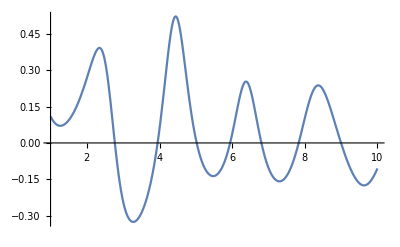

```mathematica
Plot[DipoleV2LargeN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y],{k,1,10}]
```

### Manipulate

```mathematica
ClearAll[time,tabLarge];
time=AbsoluteTime[];
tabLarge=Table[
ClearAll[x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y];
bx=0;
x1x=bx+rA/2 Cos[rAθ];
x1y=by+rA/2 Sin[rAθ];
x2x=bx-rA/2 Cos[rAθ];
x2y=by-rA/2 Sin[rAθ];
x3x=rB/2 Cos[rBθ];
x3y=rB/2 Sin[rBθ];
x4x=-rB/2 Cos[rBθ];
x4y=-rB/2 Sin[rBθ];
{{k,by,rA,rB,rAθ,rBθ},DipoleV2LargeN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]},
{k,1,10,0.1},{by,0,5,1(*0.1*)},{rA,0.1,4,1(*0.2*)},{rB,0.1,4,1(*0.2*)},{rAθ,π/10,2π,π/2},{rBθ,π/10,2π,(*0.1*)π/2}]//Quiet;
AbsoluteTime[]-time
```

506.8201271

```mathematica
Flatten[tabLarge,1]
```

{1,2,{3}}

```mathematica
ClearAll[tabLarge1];
tabLarge1=Flatten[tabLarge,5];
```

```mathematica
ClearAll[tabLargeFun];
tabLargeFun=Interpolation[tabLarge1/.Indeterminate:>$Failed,InterpolationOrder->1];
```

```mathematica
Manipulate[{Show[Graphics[{Red,Disk[{rA/2 Cos[rAθ],by+rA/2 Sin[rAθ]},0.08]}],Graphics[{Blue,Disk[{-rA/2 Cos[rAθ],by-rA/2 Sin[rAθ]},0.08]}],Graphics[Line[{{rA/2 Cos[rAθ],by+rA/2 Sin[rAθ]},{-rA/2 Cos[rAθ],by-rA/2 Sin[rAθ]}}]],Graphics[{Red,Thick,Circle[{rB/2 Cos[rBθ],rB/2 Sin[rBθ]},0.08]}],Graphics[{Blue,Thick,Circle[{-rB/2 Cos[rBθ],-rB/2 Sin[rBθ]},0.08]}],Graphics[Line[{{rB/2 Cos[rBθ],rB/2 Sin[rBθ]},{-rB/2 Cos[rBθ],-rB/2 Sin[rBθ]}}]],Graphics[{Dashed,Line[{{0,0},{0,by}}]}],PlotRange->{{-3,3},{-3,8}},ImageSize->Medium,Frame->True],Plot[tabLargeFun[k,by,rA,rB,rAθ,rBθ],{k,1,10},PlotRange->{{1,10},{-0.5,0.5}},Frame->True,FrameLabel->{"kT","v_2"},ImageSize->Large]},{by,0,5,1(*0.1*)},{rA,0.1,4,1(*0.2*)},{rB,0.1,4,1(*0.2*)},{rAθ,π/10,3/2 π+π/10,π/2},{rBθ,π/10,3/2 π+π/10,(*0.1*)π/2}]//Quiet
```

### b

```mathematica
Getv2kT[k_,b_,rA_,rAθ_,rB_,rBθ_]:=Module[{bx,by,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y},
bx=b;
by=0.0;
x1x=bx/2+rA/2 Cos[rAθ];
x1y=by/2+rA/2 Sin[rAθ];
x2x=bx/2-rA/2 Cos[rAθ];
x2y=by/2-rA/2 Sin[rAθ];
x3x=-bx/2+rB/2 Cos[rBθ];
x3y=-by/2+rB/2 Sin[rBθ];
x4x=-bx/2-rB/2 Cos[rBθ];
x4y=-by/2-rB/2 Sin[rBθ];
DipoleV2LargeN[k,x1x,x1y,x2x,x2y,x3x,x3y,x4x,x4y]
]
```

## b = 2

```mathematica
v2b20={{0.25,{-0.06294322741979848,-5.872321911797908*^-14}},{0.5,{-0.24189847126191794,-9.807551961406356*^-14}},{0.75,{-0.48454430255054487,2.2667164790300553*^-12}},{1.,{-0.6800785363396218,3.4978220482221835*^-16}},{1.25,{-0.7220912766079246,2.4983846780752516*^-16}},{1.5,{-0.650731830888267,-1.1387042913052963*^-16}},{1.75,{-0.5698212354744296,7.270017905940325*^-9}},{2.,{-0.5208747233243994,-4.962528455771066*^-11}},{2.25,{-0.5038285007534246,2.572975163973258*^-16}},{2.5,{-0.5108651725283526,-3.6685740814896163*^-17}},{2.75,{-0.5359088562216001,1.0752769076388552*^-17}},{3.,{-0.5747349714667126,-5.156639452737525*^-11}},{3.25,{-0.6231660710887356,-5.5260154113042726*^-11}},{3.5,{-0.6747391729334864,-4.817749058863643*^-9}},{3.75,{-0.7181193014223666,-5.096793214093726*^-16}},{4.,{-0.7356515260639354,4.562421243460781*^-11}},{4.25,{-0.7068377906836053,1.5812152705665003*^-10}},{4.5,{-0.6200397671962029,-2.961058277449802*^-10}},{4.75,{-0.48578306524934883,9.089602848604425*^-10}},{5.,{-0.334779210077128,7.184618206596412*^-10}},{5.25,{-0.19940392339034865,6.109210383218498*^-10}},{5.5,{-0.09862110608487162,1.1568971325936654*^-10}},{5.75,{-0.037629584808339014,-1.59247211137254*^-7}},{6.,{-0.014591830726602193,-7.964591998488446*^-8}},{6.25,{-0.02589113512522865,-8.520396403330992*^-9}},{6.5,{-0.06648030216450584,5.121406215487558*^-9}},{6.75,{-0.12219534081661644,4.675102462664738*^-9}},{7.,{-0.1506596938977829,-6.653650617568884*^-9}},{7.25,{-0.08351907572346967,-7.279697153350364*^-9}},{7.5,{0.07351684868684566,-7.187975099852266*^-7}},{7.75,{0.21315703822109988,-4.768282588361576*^-9}},{8.,{0.2794788117447774,4.509993543480511*^-9}},{8.25,{0.28354887557304587,3.4201174803693674*^-7}},{8.5,{0.24410348740864138,3.2793812314154096*^-9}},{8.75,{0.16975516203657443,1.3941639784470171*^-8}},{9.,{0.06115678697680605,-6.158505198188955*^-9}},{9.25,{-0.08326507912618733,1.1007489713600945*^-9}},{9.5,{-0.2571210409856718,-2.693396891221436*^-8}},{9.75,{-0.42852210021658116,8.656653418891017*^-9}},{10.,{-0.530749482927675,1.1991728842356803*^-8}},{10.25,{-0.5054459829067915,-2.28123805971069*^-8}},{10.5,{-0.37253524526226967,4.518471010902129*^-9}},{10.75,{-0.20791915697739471,-3.6464296097760344*^-8}},{11.,{-0.0682471797412982,1.9037880247406803*^-8}},{11.25,{0.027885219884035483,7.195414216127103*^-9}},{11.5,{0.08099214076241602,-2.9519283867048526*^-8}},{11.75,{0.09531902142089092,-1.539245176228123*^-8}},{12.,{0.07303150974721256,-7.584466563659315*^-8}},{12.25,{0.01390534016913221,-1.3338237891310884*^-7}},{12.5,{-0.0790213103481187,-1.4255344027088598*^-7}},{12.75,{-0.18233380986642045,-9.246313273463266*^-9}},{13.,{-0.23149069368658604,-7.385189219620484*^-9}},{13.25,{-0.1631330325050519,0.000011533849127017156}},{13.5,{-0.014349447755094754,4.307972012870345*^-8}},{13.75,{0.12469871960484381,1.1005108650760391*^-7}},{14.,{0.21272690232622468,-7.47863493307385*^-8}},{14.25,{0.24954399283555537,3.955983105976257*^-7}},{14.5,{0.24296605442241073,6.184276638840328*^-8}},{14.75,{0.19686064928461325,-3.1443103914760433*^-7}},{15.,{0.11068912238492895,2.902138022082587*^-8}},{15.25,{-0.01563043014371366,-2.8991147563658828*^-8}},{15.5,{-0.1700461276571382,1.4290615423408356*^-8}},{15.75,{-0.3134205946534458,-3.6586914747695166*^-7}},{16.,{-0.3858421202211369,-5.599714401436502*^-7}},{16.25,{-0.35708125713994454,-1.455416319384827*^-7}},{16.5,{-0.2582446192832246,9.487655565974058*^-8}},{16.75,{-0.14268739967635663,-3.08041240584178*^-7}},{17.,{-0.044339135713777976,-4.951558803240745*^-7}},{17.25,{0.02461714514783369,-1.8506868489498085*^-7}},{17.5,{0.06258721953101362,1.6448695112724287*^-7}},{17.75,{0.0705554180522356,8.380290820798926*^-7}},{18.,{0.04966711758307086,1.0715545063814352*^-6}},{18.25,{0.002709486448495187,8.974236072697144*^-7}},{18.5,{-0.06020492901229033,2.141314165578874*^-6}},{18.75,{-0.11442086492902735,-2.5253281268175955*^-6}},{19.,{-0.12558534475834957,-5.623738938645738*^-6}},{19.25,{-0.07835197700979778,-1.816825529239655*^-6}},{19.5,{0.00548526005581421,-6.651141506008074*^-7}},{19.75,{0.09071369124051476,-1.2673220496216533*^-6}},{20.,{0.1547768904773603,2.4172920017137556*^-7}},{20.25,{0.18966365468653157,8.794934170998154*^-9}},{20.5,{0.19368400332001778,5.738993216011659*^-7}},{20.75,{0.16666954012832896,-2.2986127464561347*^-7}},{21.,{0.10959022250044127,-5.666023778862234*^-7}},{21.25,{0.028194659156818406,-6.130940827120786*^-7}},{21.5,{-0.06340099040738281,8.730536472610196*^-7}},{21.75,{-0.14243897513144396,3.133458694315894*^-6}},{22.,{-0.18785308061251765,7.078895193830209*^-7}},{22.25,{-0.19316964458001137,-2.7821864462356767*^-6}},{22.5,{-0.16721112714985586,-9.433836998008276*^-7}},{22.75,{-0.12611941980518482,5.683253342228982*^-6}},{23.,{-0.08276295845798627,4.12023584865759*^-6}},{23.25,{-0.0452933207156625,-0.00004570340855019165}},{23.5,{-0.017735331742114287,-9.075615787723264*^-6}},{23.75,{-0.0014710078976876248,-7.711380419536145*^-7}},{24.,{0.004207762544797663,1.6392459718001695*^-6}},{24.25,{0.0019640140411407024,4.057027062705144*^-7}},{24.5,{-0.0036413484619243746,6.981744394960065*^-6}},{24.75,{-0.007074661146851558,8.224059001514674*^-6}},{25.,{-0.0038186068467083284,0.00003589812211751707}},{25.25,{0.007129402564893433,-0.0000100276432169617}},{25.5,{0.02622177591886605,-4.671121772801215*^-6}},{25.75,{0.04948317887911058,7.1686424044688035*^-6}},{26.,{0.07303292986617704,4.017299343340596*^-6}},{26.25,{0.0929312730670476,-0.000017154247732977316}},{26.5,{0.10561725321750384,-9.921865846817033*^-6}},{26.75,{0.10820024775092153,8.40263122427552*^-6}},{27.,{0.09912637011676095,0.00003315702779153328}},{27.25,{0.07861467277877875,0.00001830087660803843}},{27.5,{0.04854287192025461,-0.000017289939845689203}},{27.75,{0.011738626857271613,-3.4299906116457035*^-6}},{28.,{-0.028715192370927428,6.704084108510185*^-6}},{28.25,{-0.0694833421654259,-5.803150650880738*^-6}},{28.5,{-0.10681721328848023,7.264025347662797*^-6}},{28.75,{-0.13581403182319846,-5.498983693225244*^-6}},{29.,{-0.15078108183839106,-0.00001185452562217052}},{29.25,{-0.146785231134886,2.09209154841429*^-6}},{29.5,{-0.12215070230737883,-0.000030358145685716664}},{29.75,{-0.0808648199011981,-0.000028040786433457567}},{30.,{-0.03211246877109101,0.000010650899384681635}}};
```

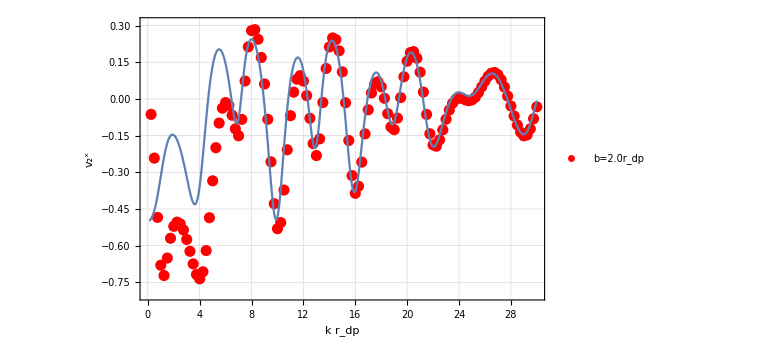

```mathematica
Show[{ListLinePlot[{Transpose[{v2b20[[All,1]],Re[v2b20[[All,2,1]]]}]},PlotRange->{{0,30},{-0.8,0.31}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"b=2.0r_dp","b=0.5r_dp","b=1.0r_dp","b=1.5r_dp","b=2.0r_dp"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k r_dp","v_2^x"}],Plot[Getv2kT[k,2.0,1.0,π/2,1.0,π/2],{k,.1,30}]}]
```

```mathematica
Length[v2b20]
```

120

```mathematica
Table[{v2b20[[All,1,i]],Re[v2b20[[All,2,1,i]]-Getv2kT[v2b20[[All,1,i]],2.0,1.0,π/2,1.0,π/2]]},{i,1,Length[v2b20]}]
```

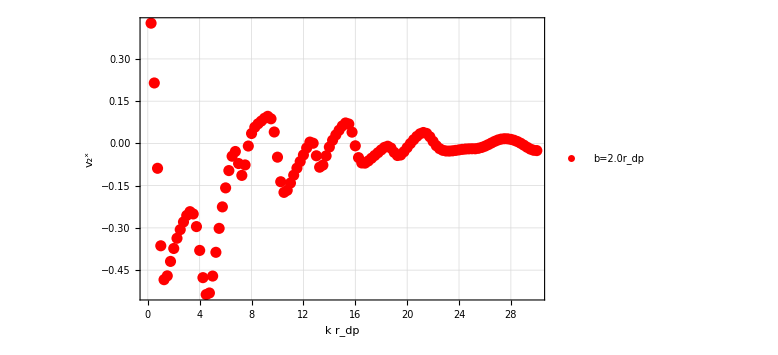

```mathematica
ListLinePlot[Table[{v2b20[[All,1]][[i]],Re[v2b20[[All,2,1]][[i]]-Getv2kT[v2b20[[All,1]][[i]],2.0,1.0,π/2,1.0,π/2]]},{i,1,Length[v2b20]}],(*PlotRange->{{0,30},{-0.8,0.31}},*)
GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"b=2.0r_dp","b=0.5r_dp","b=1.0r_dp","b=1.5r_dp","b=2.0r_dp"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k r_dp","v_2^x"}]
```

## b=1

### r_dp=0.1 b

```mathematica
v2kTr01={{0.125,{-0.003918057710614559,9.244854885711647*^-15}},{0.25,{-0.015718719721257,4.455768613178577*^-15}},{0.375,{-0.035404393455990855,-3.24942552743455*^-14}},{0.5,{-0.06282700520498571,-9.209262174235287*^-12}},{0.625,{-0.09764251133096699,1.1323373487828947*^-11}},{0.75,{-0.13932777556625237,-2.0075541724325464*^-13}},{0.875,{-0.1871596950255955,3.6587891032648094*^-14}},{1.,{-0.2402268659614949,1.7761272106741705*^-12}},{1.125,{-0.29741608683685067,1.63936386445259*^-12}},{1.25,{-0.35738980707365536,-2.9331080873408746*^-14}},{1.375,{-0.41860210294753264,5.5624657311130876*^-14}},{1.5,{-0.4792613331839505,2.1483054629612167*^-11}},{1.625,{-0.5374405029017671,-4.33280410886713*^-12}},{1.75,{-0.5910905844362639,7.782502667849232*^-10}},{1.875,{-0.6382657283683378,-1.6304778766370707*^-13}},{2.,{-0.6773485071187965,-1.1020930550360381*^-13}},{2.125,{-0.7070922567638241,-2.2980585681298934*^-14}},{2.25,{-0.7269659742677628,2.704041641059906*^-14}},{2.375,{-0.7371361605396004,6.273889630496712*^-14}},{2.5,{-0.7384228508900981,1.0598538605139731*^-13}},{2.625,{-0.7321427588980837,6.659595237400903*^-14}},{2.75,{-0.7199432377360689,-4.260275997313958*^-14}},{2.875,{-0.7034905063569131,-5.247259673659533*^-15}},{3.,{-0.6844423879210192,-2.1853706117116236*^-10}},{3.125,{-0.6641124978889632,2.067040341464235*^-7}},{3.25,{-0.6437348216121175,-1.2554414576815327*^-6}},{3.375,{-0.6240287203305982,2.3379570679486058*^-9}},{3.5,{-0.6056977704518648,-1.7925891529668374*^-14}},{3.625,{-0.5890209403411332,3.1520035514624035*^-15}},{3.75,{-0.5743230810965477,-4.1466113956369136*^-14}},{3.875,{-0.5615908182140499,3.648522336489531*^-14}},{4.,{-0.5509450813004367,1.7927726800391485*^-14}},{4.125,{-0.5422263685405077,1.0903453666383883*^-14}},{4.25,{-0.535463471178256,1.70266968146611*^-14}},{4.375,{-0.5304417121950176,4.759113761210206*^-14}},{4.5,{-0.5271569742812412,3.128951738783436*^-14}},{4.625,{-0.5253862269155424,3.598453744249841*^-14}},{4.75,{-0.5251213439483727,-2.428438280829479*^-15}},{4.875,{-0.5261507000273551,2.740499076043137*^-14}},{5.,{-0.5284673400166482,2.3894269069901594*^-14}},{5.125,{-0.5318829019586997,1.149190308111416*^-15}},{5.25,{-0.5363884128225829,2.1134322259835257*^-8}},{5.375,{-0.5418199157681947,1.2010731556825687*^-14}},{5.5,{-0.5481620285702847,1.1148763365957442*^-14}},{5.625,{-0.5552737445041922,-8.207069955019638*^-15}},{5.75,{-0.5631222515577617,5.397564812856081*^-15}},{5.875,{-0.5715864634218168,7.414484970014047*^-15}},{6.,{-0.5806247305756812,4.77842247006239*^-15}},{6.125,{-0.5901175885917581,1.3616455397502957*^-14}},{6.25,{-0.6000091086421262,4.352458936126006*^-15}},{6.375,{-0.6101831594975383,6.646937432759431*^-15}},{6.5,{-0.6205652794316837,-3.958075861245624*^-15}},{6.625,{-0.6310351690619019,-0.000018677847951257842}},{6.75,{-0.641511244041416,4.962331055710025*^-15}},{6.875,{-0.6518606611667205,2.554591094168787*^-15}},{7.,{-0.6619780296717406,1.0836216739777441*^-14}},{7.125,{-0.6717382011865476,-2.9290169948253282*^-15}},{7.25,{-0.6810190635678771,1.3639273580277793*^-14}},{7.375,{-0.6896961869618619,6.943860915145641*^-15}},{7.5,{-0.6976424505607638,-1.318541182628416*^-14}},{7.625,{-0.7047345966199451,5.447913040411827*^-15}},{7.75,{-0.7108584400080679,-2.0925760370717457*^-14}},{7.875,{-0.7159012569390238,-9.91784094948124*^-15}},{8.,{-0.7197674742523701,-1.2440075599238084*^-15}},{8.125,{-0.7223729235444168,1.0561550325913656*^-14}},{8.25,{-0.7236530530050557,-1.3847475036530753*^-14}},{8.375,{-0.7235617043911938,-1.0385721845199884*^-6}},{8.5,{-0.7220755757408699,2.287960614425298*^-14}},{8.625,{-0.7192036223031588,-8.35843469193545*^-15}},{8.75,{-0.7149657237731009,2.027975084614235*^-6}},{8.875,{-0.7094169934332586,-5.231311626546625*^-15}},{9.,{-0.7026313798074314,1.2891481340484175*^-7}},{9.125,{-0.6947167039601682,-2.147836268823866*^-14}},{9.25,{-0.685777837770821,7.096383091306253*^-15}},{9.375,{-0.676018020597335,5.709536337482595*^-10}},{9.5,{-0.6654285735792814,-8.581145590162497*^-8}},{9.625,{-0.654289558294374,4.160395754737705*^-9}},{9.75,{-0.6427632459378138,1.7996043544820085*^-9}},{9.875,{-0.6309636673004227,4.226048165496085*^-10}},{10.,{-0.6191110639479821,7.595792922208492*^-9}},{10.125,{-0.6072917387608915,-2.638841929245373*^-9}},{10.25,{-0.5957188246440015,-3.1015597792991535*^-9}},{10.375,{-0.5844645343467849,-1.551269967745795*^-8}},{10.5,{-0.57370150503722,-4.4371818780436207*^-7}},{10.625,{-0.5635097362380815,1.8552656231098774*^-9}},{10.75,{-0.5539916214788152,4.0395969162598574*^-14}},{10.875,{-0.5452226924354484,-1.780511057889443*^-14}},{11.,{-0.5372698734812158,-4.744145593705214*^-9}},{11.125,{-0.5301790327086909,4.195848666449436*^-14}},{11.25,{-0.5239872611307822,2.728685607364563*^-14}},{11.375,{-0.5187128507420379,2.4422684108623936*^-14}},{11.5,{-0.5143725975494813,-3.496286680063301*^-14}},{11.625,{-0.510955748904712,-2.0664917798758742*^-14}},{11.75,{-0.5084597678727364,2.7881696845516474*^-14}},{11.875,{-0.5068530909992728,3.1142175367135745*^-14}},{12.,{-0.5061075684239557,-1.461442305709657*^-14}},{12.125,{-0.5061716891195183,4.0825170656166505*^-14}},{12.25,{-0.5070213530125814,2.1860598265125716*^-14}},{12.375,{-0.5085695649902339,5.423487024647039*^-14}},{12.5,{-0.510777510724057,-3.7298607318384654*^-14}},{12.625,{-0.5135580520205365,-2.7144829964143545*^-14}},{12.75,{-0.516843769387631,3.905077961491842*^-14}},{12.875,{-0.5205564772213358,-5.953200852970119*^-6}},{13.,{-0.5246091726286898,2.113148931274359*^-14}},{13.125,{-0.5289076310929574,-1.2054313735626946*^-14}},{13.25,{-0.5333844134675617,2.883326672743894*^-15}},{13.375,{-0.5379172659817382,3.56506201745071*^-14}},{13.5,{-0.5424269721690292,-5.1064580363419865*^-14}},{13.625,{-0.546815862479167,-3.2318346559616534*^-14}},{13.75,{-0.551003726867789,2.1615203883493048*^-6}},{13.875,{-0.5548861803313295,6.620780524955221*^-14}},{14.,{-0.5584008919648269,-5.688665305842023*^-9}},{14.125,{-0.5614709362637526,-2.897494281422422*^-9}},{14.25,{-0.5639898471470772,-4.1928217124719556*^-14}},{14.375,{-0.5659324345221263,-3.4531692542762257*^-14}},{14.5,{-0.5672586242649905,-4.807176917575697*^-14}},{14.625,{-0.5679067183134074,2.4104502828648115*^-14}},{14.75,{-0.5678747986966025,4.710647930983182*^-14}},{14.875,{-0.5671169769243197,3.72258226325579*^-14}},{15.,{-0.5656816070173624,8.06852755841809*^-15}},{15.125,{-0.5635384254091744,-7.510508136295701*^-14}},{15.25,{-0.56075552551836,1.25152175074836*^-14}},{15.375,{-0.5573004513694695,3.5590212147582575*^-14}},{15.5,{-0.5533341837568391,9.577606751690335*^-10}},{15.625,{-0.5488184443536331,-4.8080410027081485*^-14}},{15.75,{-0.5438728526359264,-9.584287837352239*^-15}},{15.875,{-0.5385484248118637,9.3955412023375*^-8}},{16.,{-0.5329268665170057,-3.8792326671220296*^-15}},{16.125,{-0.527067341734732,4.655757932398242*^-14}},{16.25,{-0.5211152931915697,-6.7995068199288484*^-15}},{16.375,{-0.5150812721601088,5.548916646547927*^-9}},{16.5,{-0.5091125901884977,8.011336983399773*^-14}},{16.625,{-0.503210597506499,2.7218779042229064*^-7}},{16.75,{-0.49750694351250224,-3.772022823975667*^-14}},{16.875,{-0.4920537949899836,-1.2511884263301538*^-14}},{17.,{-0.48691881104524515,-5.345949023786466*^-14}},{17.125,{-0.4821307158749294,-7.410663561568436*^-15}},{17.25,{-0.47777045845568183,3.7434932908790614*^-15}},{17.375,{-0.47384415636903865,5.966703863615523*^-15}},{17.5,{-0.4704211495107554,7.532302330341834*^-14}},{17.625,{-0.46749090679274174,4.390700693813543*^-14}},{17.75,{-0.4651098856213215,-4.735876892443972*^-15}},{17.875,{-0.46324289313407163,-2.104956549555236*^-8}},{18.,{-0.4619286731818374,-4.030065275947804*^-14}},{18.125,{-0.461149077605719,-6.542881813006678*^-14}},{18.25,{-0.460895788762363,2.940479971703702*^-6}},{18.375,{-0.46113375363503656,-1.980772529508429*^-14}},{18.5,{-0.461883473081167,-2.0897297555967427*^-14}},{18.625,{-0.46307099222403986,6.681066146310082*^-14}},{18.75,{-0.46468060214693285,-1.177628293229202*^-14}},{18.875,{-0.4666571776539901,-1.7086602708282606*^-8}},{19.,{-0.46896956430538544,-3.828063149989548*^-14}},{19.125,{-0.4715519322773859,1.2322568083549429*^-14}},{19.25,{-0.4743706366449681,1.8680041343858585*^-14}},{19.375,{-0.4773503356144509,9.278299313068467*^-14}},{19.5,{-0.480430334113364,1.0318391124324963*^-13}},{19.625,{-0.4835823912600917,-5.14004639915888*^-14}},{19.75,{-0.4866998422630719,-1.7287423727555124*^-14}},{19.875,{-0.4897457666307268,-1.597230991496991*^-14}},{20.,{-0.4926391948866737,-3.25636684229374*^-6}},{20.125,{-0.4953630392999924,7.63791365314107*^-15}},{20.25,{-0.4978198385421389,-7.17621977032122*^-14}},{20.375,{-0.4999851266323586,-1.5741426666256957*^-14}},{20.5,{-0.5017369547339656,9.254957801709921*^-15}},{20.625,{-0.5031636579503245,-4.2779378693736176*^-14}},{20.75,{-0.5041334259129382,-4.9393755943928894*^-8}},{20.875,{-0.5046489107715457,4.76288951391161*^-8}},{21.,{-0.5046801237408688,5.344459368659944*^-8}},{21.125,{-0.504223877709701,-5.5449739133984515*^-8}},{21.25,{-0.5032732619523007,6.489640882211827*^-14}},{21.375,{-0.5018302417174715,-6.033401053662525*^-14}},{21.5,{-0.49992571609102104,6.127152660289473*^-8}},{21.625,{-0.49755516133334904,6.920669434659163*^-14}},{21.75,{-0.4947798164341914,8.203047498184611*^-15}},{21.875,{-0.49159876889154186,3.7752479276997184*^-14}},{22.,{-0.4880890150013355,2.6180097567770878*^-8}},{22.125,{-0.4842748163077433,-5.5482811489787554*^-14}},{22.25,{-0.4802293154570574,-5.377307437107822*^-14}},{22.375,{-0.4759754602071142,3.364912282960911*^-14}},{22.5,{-0.471635866831603,-2.3764486157273692*^-8}},{22.625,{-0.4671447714425382,-1.3016389315369388*^-13}},{22.75,{-0.46268986296936804,-7.619666953358566*^-8}},{22.875,{-0.45823245579980426,-8.475776061132287*^-8}},{23.,{-0.45388331389909664,-4.358226719250919*^-14}},{23.125,{-0.4496261773431517,1.2981206420934466*^-13}},{23.25,{-0.4457326712051796,9.618772204798758*^-8}},{23.375,{-0.44191434974351523,-1.3708939314195487*^-6}},{23.5,{-0.4384057757477033,-6.452133754270889*^-8}},{23.625,{-0.4352000848031097,4.343737142225139*^-15}},{23.75,{-0.4323384936006302,-2.374703016560287*^-13}},{23.875,{-0.4298464001530676,-2.6835303414091216*^-6}},{24.,{-0.42774329253115484,-9.237924090252065*^-8}},{24.125,{-0.4260122730013701,-1.6037490877630148*^-13}},{24.25,{-0.4247031567019669,4.409930619066391*^-14}},{24.375,{-0.42376795667412026,6.273343426917469*^-14}},{24.5,{-0.4232523021784899,-1.1754861454399368*^-14}},{24.625,{-0.42311307956741384,3.0058374124292336*^-7}},{24.75,{-0.4233649059889497,3.092283985634873*^-7}},{24.875,{-0.42392298901895437,-2.368480464842721*^-14}},{25.,{-0.42485047255910835,-3.946606557341267*^-14}},{25.125,{-0.42606027925299195,-3.282572556989622*^-7}},{25.25,{-0.42755088604521085,5.4730319659071236*^-17}},{25.375,{-0.4292463383192781,-1.1874230210186027*^-14}},{25.5,{-0.4311171000966129,-7.256387564780687*^-15}},{25.625,{-0.43314686190293206,-1.2070281234177507*^-7}},{25.75,{-0.43529145102834615,-2.881805837704058*^-14}},{25.875,{-0.4374557756665144,-2.9449024212099173*^-8}},{26.,{-0.43957192800694617,-1.2197409264483674*^-14}},{26.125,{-0.441722961502819,4.654125022016889*^-8}},{26.25,{-0.443750308925389,-1.4635979953332415*^-8}},{26.375,{-0.44560321163111033,7.768982996323666*^-7}},{26.5,{-0.44727461468616014,-1.2411452655714186*^-6}},{26.625,{-0.44871350918640085,-1.5656745865351604*^-8}},{26.75,{-0.44984616406922656,-2.7855840196869317*^-15}},{26.875,{-0.4507019432825056,1.6273714362356918*^-14}},{27.,{-0.45121017341818476,4.631950585133083*^-7}},{27.125,{-0.4513544106332651,-9.745103498577046*^-7}},{27.25,{-0.45111319996299515,2.4201012930772588*^-14}},{27.375,{-0.4504476558170241,-2.6488805190751227*^-14}},{27.5,{-0.44942414196121505,9.530213205262386*^-15}},{27.625,{-0.4479534600519532,-8.437836593057415*^-15}},{27.75,{-0.446122732979754,2.4679867204052903*^-14}},{27.875,{-0.4439039480821522,-1.239187635463128*^-14}},{28.,{-0.441333010915874,-2.275395158346231*^-6}},{28.125,{-0.4384324819950191,5.870473379266322*^-15}},{28.25,{-0.4352168639917436,1.819273635604562*^-14}},{28.375,{-0.43174072945042513,4.9519451179217836*^-14}},{28.5,{-0.42804991239419665,5.970586863076394*^-14}},{28.625,{-0.4241736359202971,-4.2677503346019027*^-14}},{28.75,{-0.4202032069696325,1.0879005736680512*^-14}},{28.875,{-0.41606411033910085,-2.1096354416855767*^-7}},{29.,{-0.4119681248300768,-2.643443418682811*^-7}},{29.125,{-0.40783575377292375,-7.961902697241522*^-16}},{29.25,{-0.40378988368510366,-6.465343161779006*^-9}},{29.375,{-0.3998109555466155,-3.3758241775275253*^-7}},{29.5,{-0.3960027985608335,3.622637540194912*^-7}},{29.625,{-0.39234925257912306,4.682866576419484*^-8}},{29.75,{-0.3889291027409299,2.5364903611170395*^-7}},{29.875,{-0.38574645668502355,2.704772699814783*^-7}},{30.,{-0.3828198488896162,-2.6158514875207895*^-14}}};
```

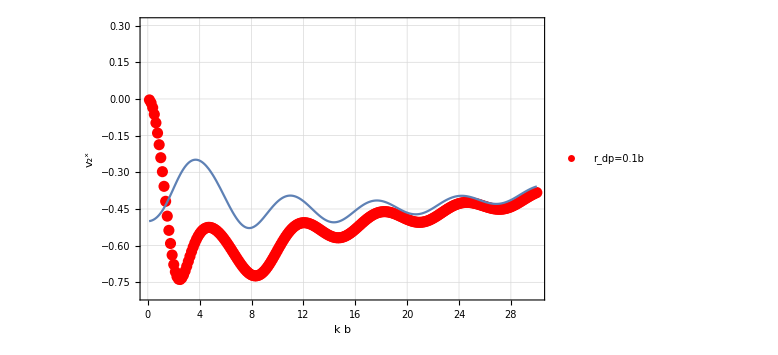

```mathematica
Show[{ListLinePlot[{Transpose[{v2kTr01[[All,1]],Re[v2kTr01[[All,2,1]]]}]},PlotRange->{{0,30},{-0.8,0.31}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"r_dp=0.1b"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k b","v_2^x"}],Plot[Getv2kT[k,1.0,0.1,π/2,0.1,π/2],{k,.1,30}]}]
```

### r_dp= b

```mathematica
v2kT={{0.125,{-0.0038145666343051333,-8.770296131118043*^-18}},{0.25,{-0.015370303774242809,1.7769218865201226*^-14}},{0.375,{-0.03478799715529221,-2.485673761449122*^-14}},{0.5,{-0.062033854653153135,1.1044824126021148*^-13}},{0.625,{-0.09688970636896405,-4.802867840181144*^-14}},{0.75,{-0.13895894530129987,1.1746760402533138*^-12}},{0.875,{-0.18767201809769854,1.3599308973306837*^-13}},{1.,{-0.24227284840377084,-3.705584516153792*^-13}},{1.125,{-0.3017631071327574,8.40659185454109*^-15}},{1.25,{-0.36479685257132444,2.03300275408307*^-10}},{1.375,{-0.4295408726611799,1.4346608999221128*^-11}},{1.5,{-0.4935462545338007,-1.3736245507186947*^-13}},{1.625,{-0.55373373845127,2.7687515447364226*^-13}},{1.75,{-0.6066027342700241,3.5199298986767468*^-12}},{1.875,{-0.6487510075044597,-7.95501088320471*^-9}},{2.,{-0.677615358940052,-7.854719824280913*^-17}},{2.125,{-0.6921638988980808,-5.877907199455664*^-17}},{2.25,{-0.6931901738297919,2.5515907936889136*^-9}},{2.375,{-0.6830488591849327,-2.7070759933888894*^-11}},{2.5,{-0.6649321089100702,-1.6542396658808482*^-11}},{2.625,{-0.6421181509627638,-7.19807111204913*^-17}},{2.75,{-0.6173983354122009,3.1894069697736614*^-10}},{2.875,{-0.5928295382586416,-8.652219940414481*^-11}},{3.,{-0.5697384783058826,-1.9024686676086125*^-11}},{3.125,{-0.5488552806539309,4.357910267936902*^-9}},{3.25,{-0.5304853678478362,-1.8187476613841656*^-8}},{3.375,{-0.514662487111251,3.205852917590607*^-11}},{3.5,{-0.5012655434825574,2.362139232379727*^-12}},{3.625,{-0.49009685235904876,1.2062354309457428*^-9}},{3.75,{-0.4809341348538826,7.728655260097078*^-11}},{3.875,{-0.4735567521374093,2.1669551987315467*^-11}},{4.,{-0.46776639040835283,2.4043099076459743*^-12}},{4.125,{-0.46338572729979044,-1.9871356255715666*^-9}},{4.25,{-0.4602694766355951,2.2842938117113635*^-9}},{4.375,{-0.4582975020517393,4.112738034263924*^-11}},{4.5,{-0.45737709848908636,-2.6459958623624444*^-10}},{4.625,{-0.45743666609035105,1.4689147078888108*^-9}},{4.75,{-0.45842964327899915,-7.484851498416402*^-9}},{4.875,{-0.46032370275658935,-2.5713707684613013*^-10}},{5.,{-0.46310779021610066,-1.3712534670396533*^-9}},{5.125,{-0.4667837438238167,-1.0239570442654021*^-10}},{5.25,{-0.47137016379617547,3.4480297702592567*^-9}},{5.375,{-0.47689639658224264,1.0185882805063667*^-8}},{5.5,{-0.48340462829858677,-1.3064862821084218*^-16}},{5.625,{-0.4909475202400304,-3.5885111347141615*^-10}},{5.75,{-0.4995850244361453,1.423344748949777*^-11}},{5.875,{-0.5093816166836549,2.987297297810001*^-12}},{6.,{-0.5204009405259216,2.7476150804417533*^-10}},{6.125,{-0.532695887360128,-5.111586286447776*^-16}},{6.25,{-0.5462945270855182,2.533566513832376*^-15}},{6.375,{-0.5611759244807163,-1.0918216923616846*^-15}},{6.5,{-0.5772326695516907,-1.9307243431914002*^-15}},{6.625,{-0.5942085617851417,6.527851703397193*^-7}},{6.75,{-0.611624941261184,-1.145481241545447*^-11}},{6.875,{-0.6286119048809296,-1.2352274845334554*^-9}},{7.,{-0.6437578704106229,-2.4689414366078834*^-11}},{7.125,{-0.6548516017335444,4.020902932626045*^-16}},{7.25,{-0.6586511454450078,-2.2671543457063428*^-10}},{7.375,{-0.6507856659168332,-4.8029998958123*^-10}},{7.5,{-0.6260948798292884,-2.906903758874852*^-10}},{7.625,{-0.5797587653386406,2.6468322330340016*^-8}},{7.75,{-0.5094436060825578,-2.8274905450754082*^-9}},{7.875,{-0.4176696638240725,1.165557385667161*^-10}},{8.,{-0.3127001568032249,-1.4984272522717237*^-10}},{8.125,{-0.20640431457964284,7.784916453572846*^-10}},{8.25,{-0.11002346166297973,1.76213080455171*^-8}},{8.375,{-0.030688480328536598,-5.073079848895744*^-10}},{8.5,{0.029396586686098465,7.266637614962103*^-9}},{8.625,{0.07162741303856758,4.798172958532609*^-8}},{8.75,{0.09911283511377558,5.15503078078277*^-8}},{8.875,{0.1152854257435328,5.150587837327192*^-9}},{9.,{0.12317100288371782,-6.3826171831989315*^-9}},{9.125,{0.1251598556590087,-3.863930324180945*^-8}},{9.25,{0.12301824022670999,-9.50091362653667*^-10}},{9.375,{0.11797926505274271,-8.726014206656516*^-10}},{9.5,{0.1109669876096405,2.620381383439199*^-10}},{9.625,{0.10249356506802704,9.218029505727073*^-10}},{9.75,{0.09293238374440915,-1.3441154978021209*^-9}},{9.875,{0.08249896886222301,-5.546269484549476*^-9}},{10.,{0.07130896973595931,8.47169445824443*^-9}},{10.125,{0.05939273342600049,6.750027719013291*^-10}},{10.25,{0.04672958171071315,4.33892282797973*^-8}},{10.375,{0.03327021167474194,2.9074247340966017*^-9}},{10.5,{0.018929582991274403,4.932907672318059*^-8}},{10.625,{0.0036110335040011156,1.92512293299272*^-8}},{10.75,{-0.012780556695824017,3.4346509102841225*^-9}},{10.875,{-0.03034027081431167,4.324260429674358*^-8}},{11.,{-0.04914309652831915,-8.798252620692403*^-10}},{11.125,{-0.06922330171874276,-2.190145471428356*^-10}},{11.25,{-0.090576688316893,6.4626269237177645*^-9}},{11.375,{-0.11311812352551533,1.0529468814856192*^-8}},{11.5,{-0.136708521058601,-1.1033906130299018*^-8}},{11.625,{-0.1610636412417012,4.242955871885293*^-11}},{11.75,{-0.18581935335879288,1.566971093523524*^-8}},{11.875,{-0.21048962466790191,6.003760530631209*^-9}},{12.,{-0.23448917168911598,9.497906648349837*^-10}},{12.125,{-0.2571550525975473,-6.831782446148319*^-8}},{12.25,{-0.27779716282642714,-1.8093309951838823*^-8}},{12.375,{-0.2957334481632961,2.3175546121128544*^-9}},{12.5,{-0.3103659708978077,3.042438163936668*^-8}},{12.625,{-0.3212096395353938,2.588294890963012*^-8}},{12.75,{-0.32794959786110156,1.952688159417017*^-8}},{12.875,{-0.33043471585181744,7.466464731199854*^-7}},{13.,{-0.3286914992406541,7.783544369806296*^-10}},{13.125,{-0.32288791563580826,1.3832461642299231*^-9}},{13.25,{-0.3133057245055995,-3.291125763139785*^-8}},{13.375,{-0.30029388605755963,-9.466693757195717*^-9}},{13.5,{-0.2842418950802804,-3.7066213982523582*^-9}},{13.625,{-0.2655358682344628,2.4052208234159764*^-9}},{13.75,{-0.24454795541806823,4.249484658791227*^-9}},{13.875,{-0.22161861851500086,-4.267003248770652*^-9}},{14.,{-0.19705760854870333,9.232773458052011*^-8}},{14.125,{-0.17115148392152654,7.230774471952747*^-11}},{14.25,{-0.14413238248873098,-6.4626660365719775*^-9}},{14.375,{-0.11627533859694629,-3.95151809436999*^-9}},{14.5,{-0.08782837791280503,9.054399528965831*^-9}},{14.625,{-0.059064600501465676,-1.815661943082681*^-8}},{14.75,{-0.030295842098810748,-1.0398767252133559*^-8}},{14.875,{-0.00187656100414676,9.564632506909921*^-8}},{15.,{0.025786526327060313,-4.4146709066272754*^-9}},{15.125,{0.05224030733121436,1.2145866373786358*^-7}},{15.25,{0.07698661849629682,-7.501192091078092*^-10}},{15.375,{0.09951677222373859,-2.395759501218834*^-7}},{15.5,{0.11931185030441603,-1.6320169373384063*^-7}},{15.625,{0.13591855458098143,2.6323438436675254*^-8}},{15.75,{0.14894312415829705,-3.9811813532938125*^-8}},{15.875,{0.15811920441716093,-6.571553518005781*^-7}},{16.,{0.16331182862433666,6.775642060945504*^-9}},{16.125,{0.16453632164043125,3.451776923005785*^-7}},{16.25,{0.16195530127928567,1.0904008548060991*^-8}},{16.375,{0.15586566820540948,-5.856106208189421*^-9}},{16.5,{0.14665473514453153,2.3944201313874438*^-8}},{16.625,{0.1347449033628869,-5.94791375086431*^-8}},{16.75,{0.1206284574361209,8.18726790090496*^-9}},{16.875,{0.10476255950741153,1.597787739307408*^-8}},{17.,{0.08757222390690272,-2.4154818888100097*^-8}},{17.125,{0.06944332511167735,-1.7255325887560422*^-8}},{17.25,{0.05069788314207085,5.209228323515558*^-9}},{17.375,{0.031602080784626285,5.3851957648149655*^-9}},{17.5,{0.012356457924273449,-8.492074884500232*^-9}},{17.625,{-0.006878400069119971,5.071649221215491*^-8}},{17.75,{-0.025992938167556212,3.2205245879034055*^-8}},{17.875,{-0.044915026683393595,2.8235149488587112*^-8}},{18.,{-0.0635915975354855,-7.180941484215929*^-8}},{18.125,{-0.08199376720334547,2.2421869553245094*^-8}},{18.25,{-0.10009379366472551,-5.7629362680555393*^-8}},{18.375,{-0.1178717396323955,-5.308192498435593*^-8}},{18.5,{-0.13528958020224263,1.2843834481107857*^-8}},{18.625,{-0.15229746178705766,1.1577887120470588*^-8}},{18.75,{-0.16880500291898254,3.0828820042084766*^-8}},{18.875,{-0.18468008243409265,4.022618542525332*^-9}},{19.,{-0.1997420713822689,1.2841134839065155*^-8}},{19.125,{-0.21372394031556527,9.339306251395149*^-9}},{19.25,{-0.22627881062030591,-8.61930011278599*^-9}},{19.375,{-0.2369575412087999,-1.4205010381434548*^-7}},{19.5,{-0.2452172603062858,-1.6140369547695166*^-8}},{19.625,{-0.2504187027300958,-2.2053764660425456*^-8}},{19.75,{-0.25186087080652686,-2.6623312486213505*^-8}},{19.875,{-0.24886432146159176,-1.8278743642287222*^-8}},{20.,{-0.24083540469107942,1.907883119889603*^-8}},{20.125,{-0.22740252143494968,-1.8959363795010147*^-8}},{20.25,{-0.20853636764698505,-1.9073111494478228*^-8}},{20.375,{-0.18464289289575359,-2.2476774938629513*^-8}},{20.5,{-0.1565706658835486,2.3200394321981184*^-8}},{20.625,{-0.1255751940461361,1.1354988784566779*^-9}},{20.75,{-0.09311662767328212,-1.6078359424170658*^-9}},{20.875,{-0.06069130510378376,-2.5510781720197452*^-8}},{21.,{-0.02964418925000249,4.008578860586756*^-8}},{21.125,{-0.0010140404149581437,-6.349580893147823*^-9}},{21.25,{0.02450334873765068,1.836253019961593*^-8}},{21.375,{0.04655469382496608,4.8848136632172036*^-9}},{21.5,{0.06505843044393464,-1.7130306603637772*^-8}},{21.625,{0.08013400717415561,-6.907034236865978*^-8}},{21.75,{0.09202558699541653,3.627621394360486*^-9}},{21.875,{0.10104344129153521,1.4669503918614154*^-8}},{22.,{0.10750560900676612,-5.252652172720938*^-8}},{22.125,{0.11172219745225771,2.5009921938664007*^-8}},{22.25,{0.11397008494126462,-1.0340229048122765*^-8}},{22.375,{0.11449078898693496,-1.345958034283419*^-7}},{22.5,{0.11346574600033521,-3.85159791992006*^-8}},{22.625,{0.1110712899168813,-9.149304463872573*^-8}},{22.75,{0.10739191788629823,-9.994343755065057*^-8}},{22.875,{0.10251885983416134,1.0651013568898881*^-7}},{23.,{0.09648263405551326,-1.8618768637936514*^-7}},{23.125,{0.08931086904126878,7.093198429341704*^-8}},{23.25,{0.0809875810098753,8.222807097935609*^-8}},{23.375,{0.07145716992352505,-1.6800102889758003*^-7}},{23.5,{0.06069747547032684,-1.9006903612493493*^-7}},{23.625,{0.04864499290638047,3.785554618475615*^-8}},{23.75,{0.035224072437261875,-1.9335605736010814*^-7}},{23.875,{0.020397904336888865,2.646037286004819*^-7}},{24.,{0.004120000250285188,3.497660527738634*^-7}},{24.125,{-0.013610565905500437,2.0090207442280426*^-7}},{24.25,{-0.03274223117264212,1.2418090260350386*^-10}},{24.375,{-0.05314638046247782,2.451838671469473*^-7}},{24.5,{-0.074589548795838,3.2636615680707444*^-7}},{24.625,{-0.09672378684794822,1.4244828000456934*^-7}},{24.75,{-0.11906174069597159,5.446074673066934*^-8}},{24.875,{-0.14097423975266055,-2.218367282414495*^-8}},{25.,{-0.16174085280010547,-1.6816166733325572*^-7}},{25.125,{-0.1805406556886541,-1.433516818957498*^-7}},{25.25,{-0.19657752903538464,-1.1347595581348781*^-7}},{25.375,{-0.20911611252246826,-1.1519862171122622*^-7}},{25.5,{-0.21760115667704305,1.0728266843237122*^-7}},{25.625,{-0.22170261856420678,2.3440341327054375*^-7}},{25.75,{-0.22135530947741341,-4.879233309556845*^-7}},{25.875,{-0.21672981391035637,-1.4218883005669763*^-7}},{26.,{-0.20822656367240502,1.218161122109372*^-7}},{26.125,{-0.19639636606724714,8.100550539477312*^-7}},{26.25,{-0.18184339390327633,-6.590028213718615*^-8}},{26.375,{-0.16519115228506792,1.3669169847766928*^-7}},{26.5,{-0.14704513769213645,2.415876776269508*^-7}},{26.625,{-0.1278768047468305,3.4425429795674145*^-7}},{26.75,{-0.10816248250822058,8.392993596909107*^-8}},{26.875,{-0.08826150384698674,4.077629036161783*^-7}},{27.,{-0.06843004873430975,1.2877566638553538*^-7}},{27.125,{-0.04888997227635365,-4.98843349273612*^-7}},{27.25,{-0.02980228240468462,1.6271806740265945*^-7}},{27.375,{-0.011298320087779614,9.842329651647929*^-8}},{27.5,{0.00651692447581312,-4.517788570104052*^-7}},{27.625,{0.023550594933635212,1.8898300969370754*^-7}},{27.75,{0.03971106544028546,2.12269775634385*^-7}},{27.875,{0.054919696076814815,2.338265396311496*^-8}},{28.,{0.06904811337710506,5.043033016240346*^-8}},{28.125,{0.08200343414429004,1.4879430408371898*^-7}},{28.25,{0.09364864844663295,1.0184164896006994*^-7}},{28.375,{0.10383615793196048,5.229567518913376*^-8}},{28.5,{0.11241161213775382,2.2229187005210472*^-7}},{28.625,{0.11921839082233468,2.4144626597174657*^-7}},{28.75,{0.12409777221326003,2.1753433556520006*^-7}},{28.875,{0.12690641346936135,2.734557337650676*^-7}},{29.,{0.12752226221839869,-1.6267679742047877*^-7}},{29.125,{0.12586645696691046,-1.9717192591996535*^-7}},{29.25,{0.1218927091839019,8.594358628600922*^-8}},{29.375,{0.11563509839763449,-2.8414361155551573*^-7}},{29.5,{0.10716956129891317,-1.0837082157693481*^-7}},{29.625,{0.09664706698571604,4.6860156403408514*^-7}},{29.75,{0.08426817499022542,1.8723369294340568*^-8}},{29.875,{0.07029714424057545,-2.7226333746782884*^-8}},{30.,{0.05501261160481038,-4.3629956338177634*^-7}}};
```

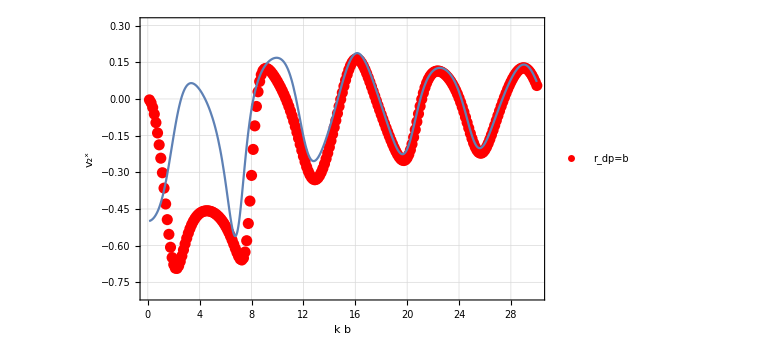

```mathematica
Show[{ListLinePlot[{Transpose[{v2kT[[All,1]],Re[v2kT[[All,2,1]]]}]},PlotRange->{{0,30},{-0.8,0.31}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"r_dp=b"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k b","v_2^x"}],Plot[Getv2kT[k,1.0,1.0,π/2,1.0,π/2],{k,.1,30}]}]
```

### r_dp= 2b

```mathematica
v2kTr2:={{0.25,{-0.011987824066760031,4.021660204770938*^-15}},{0.5,{-0.049673207241812956,3.7457278058170556*^-14}},{0.75,{-0.11478904521078691,-6.03559376280698*^-13}},{1.,{-0.21043098350362172,2.6165229794808745*^-12}},{1.25,{-0.3424213924636071,-5.932366905386802*^-11}},{1.5,{-0.4972644173674114,7.235656197835972*^-12}},{1.75,{-0.6052915303581592,1.429075244880441*^-9}},{2.,{-0.6182392496499612,-5.810031857827077*^-10}},{2.25,{-0.5781947006714055,2.591036488672839*^-9}},{2.5,{-0.5269875405595194,1.4711164766567721*^-9}},{2.75,{-0.47516016706781816,1.0229195109058451*^-10}},{3.,{-0.4202732582450019,1.0341700744266162*^-8}},{3.25,{-0.3567243229875822,-3.0597698867327406*^-9}},{3.5,{-0.2778941132463203,-2.4725129555075954*^-11}},{3.75,{-0.17664645052466302,-2.857184168460874*^-10}},{4.,{-0.04784975487476216,-1.5138502091204945*^-10}},{4.25,{0.10150396010825827,-3.034526798876663*^-10}},{4.5,{0.22858370821263108,-4.3947766735638886*^-8}},{4.75,{0.24376813124225763,1.8011667390216987*^-10}},{5.,{0.0961155046590976,-3.3259205346396855*^-9}},{5.25,{-0.1323163786505354,-8.890644432841953*^-10}},{5.5,{-0.3330770203432369,-8.738483812506843*^-11}},{5.75,{-0.4712182818271504,-5.937291443094876*^-11}},{6.,{-0.5562297130208246,3.19913796332455*^-14}},{6.25,{-0.6038322299731614,-1.343316362613863*^-10}},{6.5,{-0.6236907488011718,8.207461138109764*^-9}},{6.75,{-0.6169306558236888,-9.211967437549099*^-9}},{7.,{-0.5730402045432234,-8.644016844274223*^-9}},{7.25,{-0.46489414819364877,1.0997562851990259*^-9}},{7.5,{-0.2705239563846321,5.503309708162375*^-9}},{7.75,{-0.08788904708786317,-3.762312300738782*^-9}},{8.,{-0.06878499876237988,2.062934171328411*^-9}},{8.25,{-0.13855980875570828,2.4672428806698927*^-8}},{8.5,{-0.1972233342729097,1.8411741660851327*^-8}},{8.75,{-0.22212255068948256,-6.6979270358956116*^-9}},{9.,{-0.21488978872445233,-6.141738387451158*^-8}},{9.25,{-0.17826266524096887,-2.051531306447595*^-9}},{9.5,{-0.11309202110082736,-1.1638647567396398*^-8}},{9.75,{-0.020892587762830508,-9.865868821041999*^-9}},{10.,{0.09054919508087318,-4.2111091151572704*^-9}},{10.25,{0.19998117139037958,-2.5640980954645315*^-8}},{10.5,{0.27255893481872134,-2.5226475475485584*^-8}},{10.75,{0.2784054912830643,1.9457869988174764*^-8}},{11.,{0.21736551866818704,-1.3881977661241984*^-8}},{11.25,{0.11699320833341034,-3.669374258505795*^-8}},{11.5,{0.007946491096557571,-3.0161545891453254*^-8}},{11.75,{-0.09135122158518404,-1.5965272568449384*^-8}},{12.,{-0.1740747105500865,-2.1685916430472374*^-8}},{12.25,{-0.23921346247044006,-8.451316743334802*^-8}},{12.5,{-0.2870718920558613,-1.982937774962435*^-8}},{12.75,{-0.3169030155488351,3.5490647835805426*^-9}},{13.,{-0.32660082331163026,-2.8515596397540252*^-8}},{13.25,{-0.3150826770163598,-3.3113331079062216*^-7}},{13.5,{-0.2861269844674669,-1.1795391829366478*^-8}},{13.75,{-0.24823422412547339,2.3198299137986173*^-8}},{14.,{-0.20873437925488786,-4.389104128178838*^-8}},{14.25,{-0.16984608245571084,-4.89879500666019*^-7}},{14.5,{-0.13017560847174398,6.184682738605995*^-8}},{14.75,{-0.08784106737906038,1.6594349754732864*^-8}},{15.,{-0.04254995956358663,3.993520295392406*^-8}},{15.25,{0.0034678590094145696,7.088385296176046*^-8}},{15.5,{0.04556701897393032,-1.399729579663612*^-7}},{15.75,{0.07839062730020495,5.1250510564552584*^-8}},{16.,{0.0985327605168615,-7.632447693700044*^-8}},{16.25,{0.10639129959902074,2.0102555044861213*^-7}},{16.5,{0.10564208855686347,-8.722169067149654*^-8}},{16.75,{0.10094200603502346,4.881310529160645*^-6}},{17.,{0.09580462082990722,1.2715956523462664*^-7}},{17.25,{0.09137267296802175,-1.1139344097709211*^-6}},{17.5,{0.08591131235606088,3.630425420047259*^-7}},{17.75,{0.07453945791927896,-3.760776347009525*^-7}},{18.,{0.049675311727773105,1.8088544652417546*^-7}},{18.25,{0.0037369064960524213,-3.881291007818384*^-8}},{18.5,{-0.06487441839789523,-7.504634122237701*^-8}},{18.75,{-0.14635259854413163,1.6713926656929236*^-7}},{19.,{-0.2223394936121759,-9.855807890584442*^-7}},{19.25,{-0.2763404644149648,2.9786311794264595*^-7}},{19.5,{-0.3004303974514488,4.526143781771961*^-7}},{19.75,{-0.29383092258985205,-1.8297621045377837*^-7}},{20.,{-0.2586571861680565,-5.807329373674459*^-9}},{20.25,{-0.19791592732417773,-3.56464229241631*^-8}},{20.5,{-0.11706163713724087,-3.8378223592391937*^-7}},{20.75,{-0.027978338831833118,-2.8993007169538167*^-8}},{21.,{0.04919075632523607,3.5887682664500664*^-8}},{21.25,{0.09359462033980777,-1.6138011099817484*^-7}},{21.5,{0.09876418900096838,-3.1807042254158034*^-8}},{21.75,{0.07698132417821239,1.1399450959934535*^-7}},{22.,{0.04752343589987835,-9.03807550491679*^-7}},{22.25,{0.025186275402015297,-3.222073353158401*^-8}},{22.5,{0.017525581012597432,6.449353827038066*^-7}},{22.75,{0.027219256993020746,1.7973768565229199*^-6}},{23.,{0.054093742755611504,-2.0601498207439842*^-7}},{23.25,{0.09504526222913665,4.87946655466399*^-6}},{23.5,{0.14233277263985247,8.936711146175832*^-7}},{23.75,{0.1803055935157353,8.290006065109786*^-7}},{24.,{0.18619713545718108,1.4602462250928072*^-7}},{24.25,{0.14141327141879298,-3.555861578471053*^-7}},{24.5,{0.04958468403958911,5.688899246435387*^-7}},{24.75,{-0.06191660398742835,-9.269826118990355*^-7}},{25.,{-0.16265788629640243,-3.792930986029113*^-6}},{25.25,{-0.2352991707275503,2.3771936421729763*^-6}},{25.5,{-0.2746964410514922,-4.1879214842353814*^-7}},{25.75,{-0.2807425032978987,7.079031465806588*^-7}},{26.,{-0.2537479289747246,2.2870034183045297*^-6}},{26.25,{-0.19420002201416642,-3.1458065954475086*^-6}},{26.5,{-0.10754227412361007,5.7083808032143275*^-6}},{26.75,{-0.012285942907293974,0.000024218257661464282}},{27.,{0.05959945688628011,-5.063241915010969*^-6}},{27.25,{0.08397677527443981,3.003515512151491*^-6}},{27.5,{0.0662110869748594,5.995801804827665*^-6}},{27.75,{0.030895465767032455,-7.050118766113794*^-7}},{28.,{-0.00036248100895704556,1.6479617232993062*^-6}},{28.25,{-0.016264496121349538,-4.679407165003799*^-6}},{28.5,{-0.01253076882196341,-1.3603175297582572*^-6}},{28.75,{0.011625129787136656,1.9290280802050843*^-6}},{29.,{0.05470888192264921,3.634162647815335*^-7}},{29.25,{0.11157878799670498,1.7048071395391025*^-6}},{29.5,{0.1703340706645789,-9.567536440309049*^-6}},{29.75,{0.21088979262887256,0.00001381532986770998}},{30.,{0.21116272031491917,-2.2955058774012284*^-6}}}
```

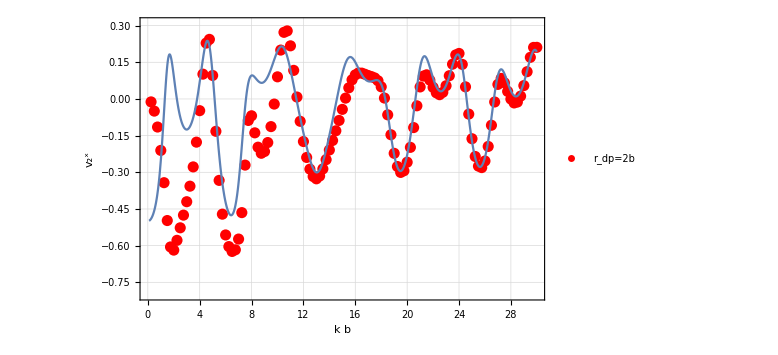

```mathematica
Show[{ListLinePlot[{Transpose[{v2kTr2[[All,1]],Re[v2kTr2[[All,2,1]]]}]},PlotRange->{{0,30},{-0.8,0.31}},GridLines->Automatic,PlotStyle->{{ -Graphics-},{ -Graphics-},{ -Graphics- },{ -Graphics-},{-Graphics-},{ -Graphics-},{ -Graphics-},{ -Graphics-},{-Graphics-},{-Graphics-}},PlotLegends->Placed[{"r_dp=2b"},{0.7,0.1}],Joined->False,ImageSize->Large,InterpolationOrder->1,Frame->True,FrameLabel->{"k b","v_2^x"}],Plot[Getv2kT[k,1.0,2.0,π/2,2.0,π/2],{k,.1,30}]}]
```